```mathematica
cm=QuantityMagnitude[UnitConvert[Quantity[1,"Centimeters"],"Inches"]]*300;
```

#### Get files

```mathematica
SetDirectory["C:\\Users\\mikol\\Dropbox\\UJ\\symulacje\\C60_Graph_hit_analysis\\data\\outputs"]
```

C:\Users\mikol\Dropbox\UJ\symulacje\C60_Graph_hit_analysis\data\outputs

```mathematica
SetDirectory["C:\\Users\\mikol\\Documents\\simulations\\Graphene_new\\Graphene_substrate\\outputs"]
```

C:\Users\mikol\Documents\simulations\Graphene_new\Graphene_substrate\outputs

```mathematica
allfilesdat=Map[
<|"path"->#,"id"->StringSplit[FileBaseName[#],"_"]|>&
,FileNames["*.dat","",Infinity]];
```

```mathematica
Length[allfilesdat]
```

55

```mathematica
allfilesdat
```

{<|path→05keV\1L\05keV_1L_00deg.dat,id→{05keV,1L,00deg}|>,<|path→05keV\2L\05keV_2L_00deg.dat,id→{05keV,2L,00deg}|>,<|path→05keV\4L\05keV_4L_00deg.dat,id→{05keV,4L,00deg}|>,<|path→05keV\6L\05keV_6L_00deg.dat,id→{05keV,6L,00deg}|>,<|path→10keV\12L\10keV_12L_00deg.dat,id→{10keV,12L,00deg}|>,<|path→10keV\1L\10keV_1L_00deg.dat,id→{10keV,1L,00deg}|>,<|path→10keV\2L\10keV_2L_00deg.dat,id→{10keV,2L,00deg}|>,<|path→10keV\4L\10keV_4L_00deg.dat,id→{10keV,4L,00deg}|>,<|path→10keV\6L\10keV_6L_00deg.dat,id→{10keV,6L,00deg}|>,<|path→10keV\8L\10keV_8L_00deg.dat,id→{10keV,8L,00deg}|>,<|path→20keV\12L\20keV_12L_00deg.dat,id→{20keV,12L,00deg}|>,<|path→20keV\16L\20keV_16L_00deg.dat,id→{20keV,16L,00deg}|>,<|path→20keV\4L\20keV_4L_00deg.dat,id→{20keV,4L,00deg}|>,<|path→20keV\6L\20keV_6L_00deg.dat,id→{20keV,6L,00deg}|>,<|path→40keV\12L\40keV_12L_00deg.dat,id→{40keV,12L,00deg}|>,<|path→40keV\16L\40keV_16L_00deg.dat,id→{40keV,16L,00deg}|>,<|path→40keV\1L\40keV_1L_00deg.dat,id→{40keV,1L,00deg}|>,<|path→40keV\4L\40keV_4L_00deg.dat,id→{40keV,4L,00deg}|>,<|path→40keV\6L\40keV_6L_00deg.dat,id→{40keV,6L,00deg}|>,<|path→impact_angle\10keV\00deg\2L\10keV_2L_00deg.dat,id→{10keV,2L,00deg}|>,<|path→impact_angle\10keV\15deg\2L\10keV_2L_15deg.dat,id→{10keV,2L,15deg}|>,<|path→impact_angle\10keV\30deg\2L\10keV_2L_30deg.dat,id→{10keV,2L,30deg}|>,<|path→impact_angle\10keV\45deg\1L\10keV_1L_45deg.dat,id→{10keV,1L,45deg}|>,<|path→impact_angle\10keV\45deg\2L\10keV_2L_45deg.dat,id→{10keV,2L,45deg}|>,<|path→impact_angle\10keV\45deg\4L\10keV_4L_45deg.dat,id→{10keV,4L,45deg}|>,<|path→impact_angle\10keV\45deg\6L\10keV_6L_45deg.dat,id→{10keV,6L,45deg}|>,<|path→impact_angle\10keV\50deg\2L\10keV_2L_50deg.dat,id→{10keV,2L,50deg}|>,<|path→impact_angle\10keV\55deg\2L\10keV_2L_55deg.dat,id→{10keV,2L,55deg}|>,<|path→impact_angle\10keV\60deg\2L\10keV_2L_60deg.dat,id→{10keV,2L,60deg}|>,<|path→impact_angle\10keV\65deg\2L\10keV_2L_65deg.dat,id→{10keV,2L,65deg}|>,<|path→impact_angle\10keV\70deg\2L\10keV_2L_70deg.dat,id→{10keV,2L,70deg}|>,<|path→impact_angle\10keV\75deg\2L\10keV_2L_75deg.dat,id→{10keV,2L,75deg}|>,<|path→impact_angle\10keV\80deg\2L\10keV_2L_80deg.dat,id→{10keV,2L,80deg}|>,<|path→impact_angle\40keV\00deg\2L\40keV_2L_00deg.dat,id→{40keV,2L,00deg}|>,<|path→impact_angle\40keV\00deg\8L\40keV_8L_00deg.dat,id→{40keV,8L,00deg}|>,<|path→impact_angle\40keV\15deg\2L\40keV_2L_15deg.dat,id→{40keV,2L,15deg}|>,<|path→impact_angle\40keV\15deg\8L\40keV_8L_15deg.dat,id→{40keV,8L,15deg}|>,<|path→impact_angle\40keV\30deg\2L\40keV_2L_30deg.dat,id→{40keV,2L,30deg}|>,<|path→impact_angle\40keV\30deg\8L\40keV_8L_30deg.dat,id→{40keV,8L,30deg}|>,<|path→impact_angle\40keV\45deg\12L\40keV_12L_45deg.dat,id→{40keV,12L,45deg}|>,<|path→impact_angle\40keV\45deg\16L\40keV_16L_45deg.dat,id→{40keV,16L,45deg}|>,<|path→impact_angle\40keV\45deg\1L\40keV_1L_45deg.dat,id→{40keV,1L,45deg}|>,<|path→impact_angle\40keV\45deg\2L\40keV_2L_45deg.dat,id→{40keV,2L,45deg}|>,<|path→impact_angle\40keV\45deg\4L\40keV_4L_45deg.dat,id→{40keV,4L,45deg}|>,<|path→impact_angle\40keV\45deg\8L\40keV_8L_45deg.dat,id→{40keV,8L,45deg}|>,<|path→impact_angle\40keV\55deg\2L\40keV_2L_55deg.dat,id→{40keV,2L,55deg}|>,<|path→impact_angle\40keV\60deg\16L\40keV_16L_60deg.dat,id→{40keV,16L,60deg}|>,<|path→impact_angle\40keV\60deg\2L\40keV_2L_60deg.dat,id→{40keV,2L,60deg}|>,<|path→impact_angle\40keV\60deg\8L\40keV_8L_60deg.dat,id→{40keV,8L,60deg}|>,<|path→impact_angle\40keV\65deg\2L\40keV_2L_65deg.dat,id→{40keV,2L,65deg}|>,<|path→impact_angle\40keV\70deg\2L\40keV_2L_70deg.dat,id→{40keV,2L,70deg}|>,<|path→impact_angle\40keV\70deg\8L\40keV_8L_70deg.dat,id→{40keV,8L,70deg}|>,<|path→impact_angle\40keV\75deg\2L\40keV_2L_75deg.dat,id→{40keV,2L,75deg}|>,<|path→impact_angle\40keV\77deg\2L\40keV_2L_77deg.dat,id→{40keV,2L,77deg}|>,<|path→impact_angle\40keV\80deg\2L\40keV_2L_80deg.dat,id→{40keV,2L,80deg}|>}

```mathematica
allfiles=Map[
<|"path"->#,"id"->StringSplit[FileBaseName[#],"_"]|>&
,FileNames["*.txt","",Infinity]];
```

```mathematica
Length[allfiles]
```

2705

```mathematica
allfiles⟦;;10⟧
```

{<|path→05keV_1L_00deg_-0.416667_0.000000_angledist.txt,id→{05keV,1L,00deg,-0.416667,0.000000,angledist}|>,<|path→05keV_1L_00deg_0.416667_0.000000_angledist.txt,id→{05keV,1L,00deg,0.416667,0.000000,angledist}|>,<|path→05keV_1L_00deg_-0.416667_0.000000_energies.txt,id→{05keV,1L,00deg,-0.416667,0.000000,energies}|>,<|path→05keV_1L_00deg_0.416667_0.000000_energies.txt,id→{05keV,1L,00deg,0.416667,0.000000,energies}|>,<|path→05keV_1L_00deg_-0.416667_0.000000_masses.txt,id→{05keV,1L,00deg,-0.416667,0.000000,masses}|>,<|path→05keV_1L_00deg_0.416667_0.000000_masses.txt,id→{05keV,1L,00deg,0.416667,0.000000,masses}|>,<|path→05keV_1L_00deg_-0.416667_0.000000_massspectrum.txt,id→{05keV,1L,00deg,-0.416667,0.000000,massspectrum}|>,<|path→05keV_1L_00deg_0.416667_0.000000_massspectrum.txt,id→{05keV,1L,00deg,0.416667,0.000000,massspectrum}|>,<|path→05keV_1L_00deg_-0.416667_0.000000_spotplot.txt,id→{05keV,1L,00deg,-0.416667,0.000000,spotplot}|>,<|path→05keV_1L_00deg_0.416667_0.000000_spotplot.txt,id→{05keV,1L,00deg,0.416667,0.000000,spotplot}|>}

```mathematica
Length[allfiles]/5//N
```

120.

```mathematica
data=<||>;
Scan[
With[{key=#["id"]⟦1;;3⟧},
If[!KeyExistsQ[data,key],
data[key]=<|
"files"-><|"massspectrum"->{},"angledist"->{},"energies"->{},"masses"->{},"spotplot"->{}|>,
"results"-><||>
|>
];
AppendTo[data[key]["files"][#["id"]⟦-1⟧],#["path"]];
]&,
allfiles]
```

```mathematica
datakeys=Keys[data];
```

```mathematica
Table[{datakeys⟦i⟧,Length[data[datakeys⟦i⟧]["files"]["massspectrum"]]},{i,Length[datakeys]}]
```

{{{05keV,1L,00deg},16},{{05keV,2L,00deg},16},{{05keV,4L,00deg},16},{{05keV,6L,00deg},12},{{10keV,12L,00deg},7},{{10keV,1L,00deg},8},{{10keV,1L,45deg},8},{{10keV,2L,00deg},51},{{10keV,2L,15deg},8},{{10keV,2L,30deg},8},{{10keV,2L,45deg},7},{{10keV,2L,50deg},8},{{10keV,2L,55deg},7},{{10keV,2L,60deg},8},{{10keV,2L,65deg},8},{{10keV,2L,70deg},8},{{10keV,2L,75deg},8},{{10keV,2L,80deg},8},{{10keV,4L,00deg},46},{{10keV,4L,45deg},8},{{10keV,6L,00deg},12},{{10keV,6L,45deg},8},{{10keV,8L,00deg},8},{{20keV,12L,00deg},7},{{20keV,16L,00deg},13},{{20keV,4L,00deg},16},{{20keV,6L,00deg},14},{{40keV,12L,00deg},7},{{40keV,12L,45deg},8},{{40keV,16L,00deg},5},{{40keV,16L,45deg},6},{{40keV,16L,60deg},5},{{40keV,1L,00deg},7},{{40keV,1L,45deg},7},{{40keV,2L,00deg},8},{{40keV,2L,15deg},7},{{40keV,2L,30deg},7},{{40keV,2L,45deg},7},{{40keV,2L,55deg},8},{{40keV,2L,60deg},8},{{40keV,2L,65deg},8},{{40keV,2L,70deg},8},{{40keV,2L,75deg},8},{{40keV,2L,77deg},6},{{40keV,2L,80deg},8},{{40keV,4L,00deg},12},{{40keV,4L,45deg},7},{{40keV,6L,00deg},7},{{40keV,8L,00deg},8},{{40keV,8L,15deg},6},{{40keV,8L,30deg},7},{{40keV,8L,45deg},8},{{40keV,8L,60deg},8},{{40keV,8L,70deg},6}}

```mathematica
Table[Length[data[datakeys⟦i⟧]["files"]["massspectrum"]],{i,Length[datakeys]}]
%//Mean//N
%%//Median//N
%%%//Total//N
```

{12,16,17,12,7,8,52,49,12,8,7,13,16,14,7,5,7,12,7,8,8,8,7,8,8,8,7,8,8,8,8,8,8,8,7,6,7,7,8,6,7,7,7,8,8,5,8,8,8,8,6,8,6,8}

10.037

8.

542.

#### Get info from prof .dat files

```mathematica
allinfo={};
Scan[
Block[{import,sampleinke,sampleinnum,samplesputke,samplesputnum,sampletranske,sampletransnum,projinke,projinnum,projsputke,projsputnum,projtranske,projtransnum,sampletransnumlayers},
import=Import[#["path"],"Table"];

sampletransnum=import⟦9,{4,6}⟧;
samplesputnum=import⟦10,{3,5}⟧;
sampleinnum=import⟦11,{4,6}⟧;
sampletranske=import⟦16,{4,6}⟧;
samplesputke=import⟦17,{3,5}⟧;
sampleinke=import⟦18,{4,6}⟧;

projtransnum=import⟦23,{3,5}⟧;
projsputnum=import⟦24,{3,5}⟧;
projinnum=import⟦25,{4,6}⟧;
projtranske=import⟦29,{3,5}⟧;
projsputke=import⟦30,{3,5}⟧;
projinke=import⟦31,{4,6}⟧;

sampletransnumlayers=Table[import⟦i,{2,4}⟧,{i,37,36+ToExpression[StringDrop[#["id"]⟦2⟧,-1]]}];

AppendTo[allinfo,<|"id"->#["id"],"numbers"-><|"sample"-><|"trans"->sampletransnum,"sput"->samplesputnum,"in"->sampleinnum,"layers"->sampletransnumlayers|>,"projectile"-><|"trans"->projtransnum,"sput"->projsputnum,"in"->projinnum|>|>,"ke"-><|"sample"-><|"trans"->sampletranske,"sput"->samplesputke,"in"->sampleinke|>,"projectile"-><|"trans"->projtranske,"sput"->projsputke,"in"->projinke|>|>|>];
]&,allfilesdat];
```

```mathematica
Table[{allinfo⟦i⟧["id"],allinfo⟦i⟧["numbers"]["sample"]["layers"]},{i,Length[allinfo]}]//MatrixForm
```

({05keV,1L,00deg} | {{21.563,0.438}}
{05keV,2L,00deg} | {{42.25,0.977},{13.25,0.281}}
{05keV,4L,00deg} | {{72.75,1.188},{37.813,1.367},{16.5,0.764},{6.75,0.393}}
{05keV,6L,00deg} | {{31.,2.489},{26.,1.273},{15.5,1.252},{9.5,0.875},{6.833,0.601},{2.833,0.441}}
{10keV,12L,00deg} | {{0.143,0.143},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.143,0.143},{0.,0.}}
{10keV,1L,00deg} | {{19.75,0.773}}
{10keV,2L,00deg} | {{33.409,1.6},{11.864,0.549}}
{10keV,4L,00deg} | {{95.283,1.466},{37.543,0.769},{16.37,0.467},{8.043,0.28}}
{10keV,6L,00deg} | {{119.583,3.18},{72.917,4.031},{41.917,1.76},{19.,0.826},{9.583,0.883},{4.917,0.543}}
{10keV,8L,00deg} | {{61.25,4.078},{51.5,2.982},{35.625,1.782},{20.125,1.329},{15.75,1.278},{7.125,0.99},{4.125,0.666},{2.125,0.581}}
{20keV,12L,00deg} | {{61.,16.857},{23.143,7.093},{17.143,6.081},{14.,5.269},{9.,2.837},{7.,3.281},{3.429,1.251},{2.143,0.738},{1.571,0.649},{1.143,0.261},{0.714,0.286},{0.429,0.202}}
{20keV,16L,00deg} | {{0.308,0.175},{0.077,0.077},{0.077,0.077},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.077,0.077},{0.,0.},{0.077,0.077},{0.,0.}}
{20keV,4L,00deg} | {{103.938,3.696},{40.188,1.32},{16.,0.996},{8.063,0.544}}
{20keV,6L,00deg} | {{159.429,6.153},{87.071,3.691},{46.714,2.172},{22.143,1.346},{11.,0.763},{4.357,0.452}}
{40keV,12L,00deg} | {{298.857,15.165},{200.714,9.411},{153.143,7.062},{107.,6.399},{75.,3.879},{50.714,2.222},{30.286,2.758},{15.143,2.132},{8.857,1.1},{3.,0.488},{2.571,0.369},{1.714,0.474}}
{40keV,16L,00deg} | {{42.2,27.088},{13.2,10.749},{12.6,11.102},{9.4,7.903},{7.2,6.704},{6.8,6.312},{3.6,3.356},{2.4,1.939},{1.2,0.583},{0.8,0.583},{0.6,0.245},{0.2,0.2},{0.2,0.2},{0.4,0.245},{0.2,0.2},{0.,0.}}
{40keV,1L,00deg} | {{15.429,0.922}}
{40keV,4L,00deg} | {{91.25,5.246},{40.667,3.026},{15.,1.376},{6.25,0.617}}
{40keV,6L,00deg} | {{176.143,11.375},{95.,7.413},{42.714,4.809},{19.571,1.152},{11.714,1.569},{4.857,0.261}}
{10keV,2L,00deg} | {{38.125,1.26},{12.,0.627}}
{10keV,2L,15deg} | {{37.625,1.451},{12.875,0.743}}
{10keV,2L,30deg} | {{50.75,2.664},{15.125,0.693}}
{10keV,1L,45deg} | {{31.375,1.068}}
{10keV,2L,45deg} | {{63.714,1.507},{19.857,1.1}}
{10keV,4L,45deg} | {{117.875,2.837},{58.125,3.044},{28.25,1.411},{9.75,0.959}}
{10keV,6L,45deg} | {{65.875,4.893},{56.75,4.839},{34.875,2.03},{20.125,0.99},{9.75,1.146},{3.875,0.766}}
{10keV,2L,50deg} | {{75.625,4.101},{22.375,0.375}}
{10keV,2L,55deg} | {{88.,2.944},{28.143,0.911}}
{10keV,2L,60deg} | {{89.,3.111},{35.625,1.487}}
{10keV,2L,65deg} | {{86.5,2.639},{35.375,1.614}}
{10keV,2L,70deg} | {{56.125,3.243},{25.375,1.558}}
{10keV,2L,75deg} | {{12.75,1.849},{8.375,1.267}}
{10keV,2L,80deg} | {{0.,0.},{0.,0.}}
{40keV,2L,00deg} | {{31.5,2.113},{10.,0.5}}
{40keV,8L,00deg} | {{262.25,6.956},{165.25,8.697},{101.25,5.105},{67.25,4.325},{29.,1.701},{13.75,1.25},{6.25,0.959},{4.25,0.75}}
{40keV,2L,15deg} | {{31.857,2.121},{10.571,0.841}}
{40keV,8L,15deg} | {{264.,13.567},{163.333,11.182},{96.5,4.884},{54.,3.215},{26.333,1.82},{13.833,1.167},{5.833,1.195},{3.333,0.558}}
{40keV,2L,30deg} | {{44.857,3.985},{13.857,0.962}}
{40keV,8L,30deg} | {{282.143,9.543},{190.571,8.434},{120.,5.74},{69.714,1.658},{37.857,2.955},{17.429,1.395},{6.571,0.369},{3.143,0.738}}
{40keV,12L,45deg} | {{197.875,17.923},{95.,8.625},{88.75,6.953},{67.25,6.681},{52.875,4.211},{30.,3.946},{18.875,1.977},{10.875,1.684},{6.125,1.141},{2.625,0.596},{1.375,0.565},{0.625,0.263}}
{40keV,16L,45deg} | {{3.,1.},{0.5,0.224},{0.,0.},{0.167,0.167},{0.5,0.342},{0.,0.},{0.167,0.167},{0.167,0.167},{0.333,0.211},{0.167,0.167},{0.,0.},{0.,0.},{0.167,0.167},{0.167,0.167},{0.,0.},{0.5,0.224}}
{40keV,1L,45deg} | {{23.857,1.455}}
{40keV,2L,45deg} | {{51.286,4.162},{17.714,1.267}}
{40keV,4L,45deg} | {{152.429,5.385},{70.714,4.524},{30.429,1.824},{11.571,1.556}}
{40keV,8L,45deg} | {{307.375,10.729},{201.5,4.044},{140.75,3.549},{90.875,3.248},{46.875,4.286},{24.375,0.625},{9.375,1.401},{3.375,0.625}}
{40keV,2L,55deg} | {{75.875,4.588},{23.125,1.941}}
{40keV,16L,60deg} | {{0.6,0.4},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.2,0.2},{0.,0.},{0.,0.},{0.,0.}}
{40keV,2L,60deg} | {{92.,5.046},{30.5,1.102}}
{40keV,8L,60deg} | {{224.375,13.833},{144.5,5.281},{115.5,3.611},{76.875,3.308},{42.625,2.044},{21.5,1.309},{10.875,1.288},{7.125,0.611}}
{40keV,2L,65deg} | {{103.625,4.504},{34.75,1.623}}
{40keV,2L,70deg} | {{118.625,4.009},{47.75,2.186}}
{40keV,8L,70deg} | {{34.,9.245},{15.167,4.922},{14.333,4.573},{7.167,3.468},{4.833,1.869},{2.,1.238},{2.,1.033},{2.,0.447}}
{40keV,2L,75deg} | {{129.75,5.888},{59.375,1.981}}
{40keV,2L,77deg} | {{104.,8.454},{48.167,2.676}}
{40keV,2L,80deg} | {{21.,4.013},{8.5,1.615}})

```mathematica
Table[{allinfo⟦i⟧["id"],allinfo⟦i⟧["ke"]["projectile"]},{i,Length[allinfo]}]//MatrixForm
```

({05keV,1L,00deg} | <|trans→{3245.6,21.5},sput→{0.,0.},in→{0.,0.}|>
{05keV,2L,00deg} | <|trans→{1840.8,22.},sput→{0.,0.},in→{0.5,0.3}|>
{05keV,4L,00deg} | <|trans→{358.4,13.8},sput→{0.,0.},in→{1.2,0.2}|>
{05keV,6L,00deg} | <|trans→{39.2,7.},sput→{2.23,1.31},in→{3.4,0.5}|>
{10keV,12L,00deg} | <|trans→{0.,0.},sput→{0.11,0.1},in→{1.9,0.1}|>
{10keV,1L,00deg} | <|trans→{7416.8,103.},sput→{0.,0.},in→{0.,0.}|>
{10keV,2L,00deg} | <|trans→{5426.2,38.9},sput→{0.43,0.21},in→{0.6,0.1}|>
{10keV,4L,00deg} | <|trans→{2071.2,38.6},sput→{0.34,0.22},in→{4.5,0.3}|>
{10keV,6L,00deg} | <|trans→{534.5,39.7},sput→{0.65,0.5},in→{2.8,0.3}|>
{10keV,8L,00deg} | <|trans→{122.6,26.7},sput→{5.41,4.88},in→{0.5,0.1}|>
{20keV,12L,00deg} | <|trans→{225.9,82.9},sput→{0.02,0.01},in→{3.3,0.3}|>
{20keV,16L,00deg} | <|trans→{108.9,42.1},sput→{0.42,0.19},in→{2.7,0.2}|>
{20keV,4L,00deg} | <|trans→{7839.5,226.3},sput→{3.73,2.58},in→{1.7,1.1}|>
{20keV,6L,00deg} | <|trans→{3608.2,124.8},sput→{0.43,0.42},in→{0.9,0.2}|>
{40keV,12L,00deg} | <|trans→{3187.5,388.5},sput→{0.23,0.2},in→{1.5,0.1}|>
{40keV,16L,00deg} | <|trans→{960.3,302.6},sput→{20.38,19.66},in→{2.6,0.3}|>
{40keV,1L,00deg} | <|trans→{34322.1,547.},sput→{0.59,0.59},in→{0.,0.}|>
{40keV,4L,00deg} | <|trans→{22290.,338.2},sput→{0.,0.},in→{0.1,0.}|>
{40keV,6L,00deg} | <|trans→{15231.4,446.1},sput→{8.21,8.08},in→{0.2,0.}|>
{10keV,2L,00deg} | <|trans→{5457.5,78.1},sput→{0.,0.},in→{0.,0.}|>
{10keV,2L,15deg} | <|trans→{5359.8,124.7},sput→{0.66,0.66},in→{0.,0.}|>
{10keV,2L,30deg} | <|trans→{4335.4,90.9},sput→{18.37,12.85},in→{0.1,0.}|>
{10keV,1L,45deg} | <|trans→{5802.2,97.8},sput→{294.13,52.66},in→{0.1,0.1}|>
{10keV,2L,45deg} | <|trans→{2843.2,130.1},sput→{299.15,63.1},in→{0.1,0.}|>
{10keV,4L,45deg} | <|trans→{569.9,43.1},sput→{291.27,59.31},in→{0.3,0.1}|>
{10keV,6L,45deg} | <|trans→{89.5,26.2},sput→{292.94,21.96},in→{0.7,0.3}|>
{10keV,2L,50deg} | <|trans→{2103.,80.4},sput→{675.9,47.09},in→{0.3,0.1}|>
{10keV,2L,55deg} | <|trans→{1489.8,47.3},sput→{1384.96,35.78},in→{15.,9.8}|>
{10keV,2L,60deg} | <|trans→{581.6,61.9},sput→{2775.95,103.31},in→{0.3,0.1}|>
{10keV,2L,65deg} | <|trans→{218.7,41.9},sput→{4732.09,83.3},in→{0.1,0.}|>
{10keV,2L,70deg} | <|trans→{58.6,20.6},sput→{6843.95,72.1},in→{0.1,0.}|>
{10keV,2L,75deg} | <|trans→{111.8,58.9},sput→{8218.86,59.05},in→{14.4,14.4}|>
{10keV,2L,80deg} | <|trans→{283.,80.3},sput→{8484.17,142.88},in→{403.5,131.2}|>
{40keV,2L,00deg} | <|trans→{30659.8,473.5},sput→{0.,0.},in→{0.,0.}|>
{40keV,8L,00deg} | <|trans→{9788.1,575.},sput→{0.47,0.47},in→{0.1,0.}|>
{40keV,2L,15deg} | <|trans→{30737.2,484.8},sput→{22.28,14.78},in→{0.,0.}|>
{40keV,8L,15deg} | <|trans→{9852.2,687.5},sput→{0.,0.},in→{0.1,0.}|>
{40keV,2L,30deg} | <|trans→{28572.4,346.2},sput→{74.06,51.7},in→{0.,0.}|>
{40keV,8L,30deg} | <|trans→{6295.2,616.4},sput→{86.24,46.55},in→{0.3,0.2}|>
{40keV,12L,45deg} | <|trans→{764.2,198.4},sput→{605.05,103.72},in→{0.9,0.3}|>
{40keV,16L,45deg} | <|trans→{183.3,86.1},sput→{580.7,185.46},in→{0.8,0.3}|>
{40keV,1L,45deg} | <|trans→{32203.7,335.5},sput→{475.46,111.89},in→{0.,0.}|>
{40keV,2L,45deg} | <|trans→{25181.7,423.1},sput→{805.19,141.81},in→{0.,0.}|>
{40keV,4L,45deg} | <|trans→{14897.1,524.3},sput→{856.87,193.24},in→{0.1,0.}|>
{40keV,8L,45deg} | <|trans→{3257.2,338.6},sput→{502.09,115.67},in→{0.1,0.}|>
{40keV,2L,55deg} | <|trans→{18753.5,556.6},sput→{2424.18,298.15},in→{0.,0.}|>
{40keV,16L,60deg} | <|trans→{293.9,216.9},sput→{4350.39,685.91},in→{0.3,0.}|>
{40keV,2L,60deg} | <|trans→{14155.6,1021.},sput→{4078.58,387.9},in→{0.,0.}|>
{40keV,8L,60deg} | <|trans→{1066.9,206.8},sput→{3755.9,214.72},in→{0.3,0.1}|>
{40keV,2L,65deg} | <|trans→{11369.,479.6},sput→{7621.57,299.07},in→{0.1,0.}|>
{40keV,2L,70deg} | <|trans→{5958.2,304.3},sput→{15602.5,516.16},in→{0.1,0.}|>
{40keV,8L,70deg} | <|trans→{139.5,76.2},sput→{13744.,474.2},in→{91.2,63.9}|>
{40keV,2L,75deg} | <|trans→{1955.,501.4},sput→{26490.,649.57},in→{0.,0.}|>
{40keV,2L,77deg} | <|trans→{724.9,192.1},sput→{32181.6,524.87},in→{0.,0.}|>
{40keV,2L,80deg} | <|trans→{109.9,91.6},sput→{37372.7,155.32},in→{0.,0.}|>)

```mathematica
EnAng2L={{"10keV","2L","00deg"},{"10keV","2L","15deg"},{"10keV","2L","30deg"},{"10keV","2L","45deg"},{"10keV","2L","50deg"},{"10keV","2L","55deg"},{"10keV","2L","60deg"},{"10keV","2L","65deg"},{"10keV","2L","70deg"},{"10keV","2L","75deg"},{"10keV","2L","80deg"},{"40keV","2L","00deg"},{"40keV","2L","15deg"},{"40keV","2L","30deg"},{"40keV","2L","45deg"},{"40keV","2L","55deg"},{"40keV","2L","60deg"},{"40keV","2L","65deg"},{"40keV","2L","70deg"},{"40keV","2L","75deg"},{"40keV","2L","77deg"},{"40keV","2L","80deg"}};
EnAng8L={{"10keV","8L","00deg"},{"40keV","8L","00deg"},{"40keV","8L","15deg"},{"40keV","8L","30deg"},{"40keV","8L","45deg"},{"40keV","8L","60deg"},{"40keV","8L","70deg"}};
Table[StringRiffle[ToString/@Flatten[Flatten[Table[Select[Table[{allinfo⟦i⟧["id"],allinfo⟦i⟧["numbers"]["sample"]["layers"]},{i,Length[allinfo]}],#⟦1⟧==EnAng8L⟦j⟧&],{j,Length[EnAng8L]}]⟦;;,;;,2⟧,1]⟦k⟧],"\t"],{k,Length[EnAng8L]}]
```

{61.25	4.078	51.5	2.982	35.625	1.782	20.125	1.329	15.75	1.278	7.125	0.99	4.125	0.666	2.125	0.581,262.25	6.956	165.25	8.697	101.25	5.105	67.25	4.325	29.	1.701	13.75	1.25	6.25	0.959	4.25	0.75,264.	13.567	163.333	11.182	96.5	4.884	54.	3.215	26.333	1.82	13.833	1.167	5.833	1.195	3.333	0.558,282.143	9.543	190.571	8.434	120.	5.74	69.714	1.658	37.857	2.955	17.429	1.395	6.571	0.369	3.143	0.738,307.375	10.729	201.5	4.044	140.75	3.549	90.875	3.248	46.875	4.286	24.375	0.625	9.375	1.401	3.375	0.625,224.375	13.833	144.5	5.281	115.5	3.611	76.875	3.308	42.625	2.044	21.5	1.309	10.875	1.288	7.125	0.611,34.	9.245	15.167	4.922	14.333	4.573	7.167	3.468	4.833	1.869	2.	1.238	2.	1.033	2.	0.447}

```mathematica
ToString/@Flatten[Flatten[Table[Select[Table[{allinfo⟦i⟧["id"],allinfo⟦i⟧["numbers"]["sample"]["layers"]},{i,Length[allinfo]}],#⟦1⟧==EnAng8L⟦j⟧&],{j,Length[EnAng8L]}]⟦;;,;;,2⟧,1]⟦2⟧]
```

{262.25,6.956,165.25,8.697,101.25,5.105,67.25,4.325,29.,1.701,13.75,1.25,6.25,0.959,4.25,0.75}

#### Get mass spectra from files

```mathematica
Scan[
Block[{massspectrum,import,topposition,bottomposition,topall,bottomall,top,bottom,toprelative,bottomrelative},
massspectrum=data[#]["files"]["massspectrum"];

import=Map[Import[#,"Table"]&,massspectrum];

topposition=Map[Flatten[Position[#,"Top"]]⟦1⟧&,import];
bottomposition=Map[Flatten[Position[#,"Bottom"]]⟦1⟧&,import];

topall=Table[import⟦i,topposition⟦i⟧+1;;bottomposition⟦i⟧-1,{1,2}⟧,{i,Length[import]}];
bottomall=Table[import⟦i,bottomposition⟦i⟧+1;;,{1,2}⟧,{i,Length[import]}];

top={};
Scan[
Scan[
With[{position=FirstPosition[top,#⟦1⟧]},
If[MissingQ[position],
AppendTo[top,#],
top⟦position⟦1⟧,2⟧+=#⟦2⟧
]
]&
,#]&
,topall];

bottom={};
Scan[
Scan[
With[{position=FirstPosition[bottom,#⟦1⟧]},
If[MissingQ[position],
AppendTo[bottom,#],
bottom⟦position⟦1⟧,2⟧+=#⟦2⟧
]
]&
,#]&
,bottomall];

toprelative=Transpose[{top⟦;;,1⟧,top⟦;;,2⟧/Max[top⟦;;,2⟧]}];
bottomrelative=Transpose[{bottom⟦;;,1⟧,bottom⟦;;,2⟧/Max[bottom⟦;;,2⟧]}];

data[#]["results"]["massspectrum"]=<|
"top"->top,
"bottom"->bottom,
"toprelative"->toprelative,
"bottomrelative"->bottomrelative
|>
]&
,datakeys]
```

#### Get yields

```mathematica
Scan[
Block[{masses, import,topposition,bottomposition,topall,bottomall,topC60,bottomC60,topGraph,bottomGraph,topC60MassYield,bottomC60MassYield,topC60NumberYield,bottomC60NumberYield,topGraphMassYield,bottomGraphMassYield,topGraphNumberYield,bottomGraphNumberYield},
masses=data[#]["files"]["masses"];

import=Map[Import[#,"Table"]&,masses];

topposition=Map[Flatten[Position[#,"Top"]]⟦1⟧&,import];
bottomposition=Map[Flatten[Position[#,"Bottom"]]⟦1⟧&,import];

topall=Table[import⟦i,topposition⟦i⟧+1;;bottomposition⟦i⟧-1,{3}⟧,{i,Length[import]}];
bottomall=Table[import⟦i,bottomposition⟦i⟧+1;;,{3}⟧,{i,Length[import]}];

topC60=Flatten[topall⟦;;,2⟧];
topGraph=Flatten[topall⟦;;,3⟧];
bottomC60=Flatten[bottomall⟦;;,2⟧];
bottomGraph=Flatten[bottomall⟦;;,3⟧];

topC60MassYield={Mean[topC60],If[Length[topC60]≥2,StandardDeviation[topC60],0]/Sqrt[Length[topC60]]};
topGraphMassYield={Mean[topGraph],If[Length[topC60]≥2,StandardDeviation[topGraph],0]/Sqrt[Length[topGraph]]};
bottomC60MassYield={Mean[bottomC60],If[Length[topC60]≥2,StandardDeviation[bottomC60],0]/Sqrt[Length[bottomC60]]};
bottomGraphMassYield={Mean[bottomGraph],If[Length[topC60]≥2,StandardDeviation[bottomGraph],0]/Sqrt[Length[bottomGraph]]};

topC60NumberYield=topC60MassYield/12.011;
topGraphNumberYield=topGraphMassYield/12.011;
bottomC60NumberYield=bottomC60MassYield/12.011;
bottomGraphNumberYield=bottomGraphMassYield/12.011;

data[#]["results"]["yield"]=<|
"topmass"-><|"C60"->topC60MassYield,"Graph"->topGraphMassYield|>,
"bottommass"-><|"C60"->bottomC60MassYield,"Graph"->bottomGraphMassYield|>,
"topnumber"-><|"C60"->topC60NumberYield,"Graph"->topGraphNumberYield|>,
"bottomnumber"-><|"C60"->bottomC60NumberYield,"Graph"->bottomGraphNumberYield|>
|>
]&
,datakeys]
```

#### Get angle distributions - with c60 and graph

```mathematica
Scan[
Block[{angledist,import,topposition,bottomposition,topall,bottomall,dphi,top,bottom,topkeys,bottomkeys,toprelative,bottomrelative,max,graphposition,c60position,graphall,c60all,graph,c60,graphkeys,c60keys,graphrelative,c60relative},
angledist=data[#]["files"]["angledist"];

import=Map[Import[#,"Table"]&,angledist];

topposition=Map[Flatten[Position[#,"Top"]]⟦1⟧&,import];
bottomposition=Map[Flatten[Position[#,"Bottom"]]⟦1⟧&,import];

graphposition=Map[Flatten[Position[#,"Graph"]]⟦1⟧&,import];
c60position=Map[Flatten[Position[#,"C60"]]⟦1⟧&,import];

topall=Table[import⟦i,topposition⟦i⟧+1;;bottomposition⟦i⟧-1⟧,{i,Length[import]}];
bottomall=Table[import⟦i,bottomposition⟦i⟧+1;;graphposition⟦i⟧-1⟧,{i,Length[import]}];

graphall=Table[import⟦i,graphposition⟦i⟧+1;;c60position⟦i⟧-1⟧,{i,Length[import]}];
c60all=Table[import⟦i,c60position⟦i⟧+1;;⟧,{i,Length[import]}];

dphi=Map[#⟦1,3⟧&,import];

top=<||>;
Scan[
Scan[
If[KeyExistsQ[top,#⟦1⟧],
top[#⟦1⟧]=top[#⟦1⟧]+PadRight[#⟦2;;⟧,30];,
top[#⟦1⟧]=PadRight[#⟦2;;⟧,30];
]&
,#]&
,topall];
topkeys=Keys[top];
top["all"]=ConstantArray[0,30];
Scan[
top["all"]=top["all"]+top[#];&
,topkeys];

topkeys=Keys[top];
Scan[
top[#]=Transpose[{Range[0,Length[top[#]]-1,1]*dphi⟦1⟧*180/π,top[#]}];&
,topkeys];

topkeys=Keys[top];
toprelative=<||>;
Scan[
If[Max[top[#]⟦;;,2⟧]==0,
max=1,
max=Max[top[#]⟦;;,2⟧]
];
toprelative[#]=Transpose[{top[#]⟦;;,1⟧,top[#]⟦;;,2⟧/max}];&
,topkeys];

bottom=<||>;
Scan[
Scan[
If[KeyExistsQ[bottom,#⟦1⟧],
bottom[#⟦1⟧]=bottom[#⟦1⟧]+PadRight[#⟦2;;⟧,30];,
bottom[#⟦1⟧]=PadRight[#⟦2;;⟧,30];
]&
,#]&
,bottomall];
bottomkeys=Keys[bottom];
bottom["all"]=ConstantArray[0,30];
Scan[
bottom["all"]=bottom["all"]+bottom[#];&
,bottomkeys];

bottomkeys=Keys[bottom];
Scan[
bottom[#]=Transpose[{Range[0,Length[bottom[#]]-1,1]*dphi⟦1⟧*180/π,bottom[#]}];&
,bottomkeys];

bottomkeys=Keys[bottom];
bottomrelative=<||>;
Scan[
If[Max[bottom[#]⟦;;,2⟧]==0,
max=1,
max=Max[bottom[#]⟦;;,2⟧]
];
bottomrelative[#]=Transpose[{bottom[#]⟦;;,1⟧,bottom[#]⟦;;,2⟧/max}];&
,bottomkeys];

graph=<||>;
Scan[
Scan[
If[KeyExistsQ[graph,#⟦1⟧],
graph[#⟦1⟧]=graph[#⟦1⟧]+PadRight[#⟦2;;⟧,30];,
graph[#⟦1⟧]=PadRight[#⟦2;;⟧,30];
]&
,#]&
,graphall];
graphkeys=Keys[graph];
graph["all"]=ConstantArray[0,30];
Scan[
graph["all"]=graph["all"]+graph[#];&
,graphkeys];

graphkeys=Keys[graph];
Scan[
graph[#]=Transpose[{Range[0,Length[graph[#]]-1,1]*dphi⟦1⟧*180/π,graph[#]}];&
,graphkeys];

graphkeys=Keys[graph];
graphrelative=<||>;
Scan[
If[Max[graph[#]⟦;;,2⟧]==0,
max=1,
max=Max[graph[#]⟦;;,2⟧]
];
graphrelative[#]=Transpose[{graph[#]⟦;;,1⟧,graph[#]⟦;;,2⟧/max}];&
,graphkeys];

c60=<||>;
Scan[
Scan[
If[KeyExistsQ[c60,#⟦1⟧],
c60[#⟦1⟧]=c60[#⟦1⟧]+PadRight[#⟦2;;⟧,30];,
c60[#⟦1⟧]=PadRight[#⟦2;;⟧,30];
]&
,#]&
,c60all];
c60keys=Keys[c60];
c60["all"]=ConstantArray[0,30];
Scan[
c60["all"]=c60["all"]+c60[#];&
,c60keys];

c60keys=Keys[c60];
Scan[
c60[#]=Transpose[{Range[0,Length[c60[#]]-1,1]*dphi⟦1⟧*180/π,c60[#]}];&
,c60keys];

c60keys=Keys[c60];
c60relative=<||>;
Scan[
If[Max[c60[#]⟦;;,2⟧]==0,
max=1,
max=Max[c60[#]⟦;;,2⟧]
];
c60relative[#]=Transpose[{c60[#]⟦;;,1⟧,c60[#]⟦;;,2⟧/max}];&
,c60keys];

data[#]["results"]["angledist"]=<|
"top"->top,
"toprelative"->toprelative,
"bottom"->bottom,
"bottomrelative"->bottomrelative,
"graph"->graph,
"graphrelative"->graphrelative,
"c60"->c60,
"c60relative"->c60relative
|>
]&
,datakeys]
```

#### Get energy distributions

```mathematica
Scan[
Block[{energies,import,topposition,bottomposition,topall,bottomall,toptotal,topinternal,toptranslational,bottomtotal,bottominternal,bottomtranslational},
energies=data[#]["files"]["energies"];

import=Map[Import[#,"Table"]&,energies];

topposition=Map[Flatten[Position[#,"Top"]]⟦1⟧&,import];
bottomposition=Map[Flatten[Position[#,"Bottom"]]⟦1⟧&,import];

topall=Table[import⟦i,topposition⟦i⟧+1;;bottomposition⟦i⟧-1⟧,{i,Length[import]}];
bottomall=Table[import⟦i,bottomposition⟦i⟧+1;;⟧,{i,Length[import]}];

toptotal=Flatten[topall⟦;;,;;,1⟧];
topinternal=Flatten[topall⟦;;,;;,2⟧];
toptranslational=Flatten[topall⟦;;,;;,3⟧];
bottomtotal=Flatten[bottomall⟦;;,;;,1⟧];
bottominternal=Flatten[bottomall⟦;;,;;,2⟧];
bottomtranslational=Flatten[bottomall⟦;;,;;,3⟧];

data[#]["results"]["energies"]=<|
"top"-><|"total"->toptotal,"internal"->topinternal,"translational"->toptranslational|>,
"bottom"-><|"total"->bottomtotal,"internal"->bottominternal,"translational"->bottomtranslational|>
|>
]&
,datakeys]
```

#### Get interesting datakeys

```mathematica
Union[datakeys⟦;;,1⟧]
```

{05keV,10keV,20keV,40keV}

```mathematica
layers={"1L","2L","4L","6L","8L","12L","16L"};
energies={"05keV","10keV","20keV","40keV"};
angles={"00deg","15deg","30deg","45deg","50deg","55deg","60deg","65deg","70deg","75deg","77deg","80deg"};
```

```mathematica
energiessweep=Table[Select[datakeys,#⟦2⟧==layers⟦i⟧&&#⟦3⟧=="00deg"&],{i,Length[layers]}];
```

```mathematica
layerssweep=Table[SortBy[Select[datakeys,#⟦1⟧==energies⟦i⟧&&#⟦3⟧=="00deg"&],Position[layers,#⟦2⟧]&],{i,Length[energies]}];
```

```mathematica
layerssweep45=Table[SortBy[Select[datakeys,#⟦1⟧==energies⟦i⟧&&#⟦3⟧=="45deg"&],Position[layers,#⟦2⟧]&],{i,Length[energies]}]//.{}->Sequence[];
```

```mathematica
anglessweep={Select[datakeys,#⟦1⟧=="10keV"&&#⟦2⟧=="2L"&],Select[datakeys,#⟦1⟧=="40keV"&&#⟦2⟧=="2L"&]};
```

#### Show yields

```mathematica
ejection=Column[
{
"Ejection - number of C atoms",
Grid[
Join[
{Join[{""},energies]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
"---",
ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
"---",
ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energies]}
],
layers⟦j⟧
],
{j,Length[layers]}
]
],
Alignment->Left,
Spacings->{2, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Ejection - number of C atoms
 | 05keV | 10keV | 20keV | 40keV
1L | C60: | 60.00±0.00
Graph: | 21.50±0.61 | C60: | 60.00±0.00
Graph: | 19.75±0.77 | C60: | ---
Graph: | --- | C60: | 59.86±0.14
Graph: | 15.43±0.92
2L | C60: | 57.00±0.32
Graph: | 55.50±1.12 | C60: | 56.67±1.13
Graph: | 48.17±1.22 | C60: | ---
Graph: | --- | C60: | 58.75±0.37
Graph: | 41.50±2.15
4L | C60: | 39.24±0.78
Graph: | 132.18±2.67 | C60: | 45.37±1.41
Graph: | 151.06±4.92 | C60: | 52.25±0.74
Graph: | 166.31±4.32 | C60: | 53.67±0.68
Graph: | 149.92±8.39
6L | C60: | 13.42±1.11
Graph: | 82.67±3.75 | C60: | 30.08±1.21
Graph: | 255.42±7.97 | C60: | 40.43±1.19
Graph: | 322.00±10.86 | C60: | 49.29±0.99
Graph: | 339.71±21.11
8L | C60: | ---
Graph: | --- | C60: | 13.00±1.16
Graph: | 167.25±6.68 | C60: | ---
Graph: | --- | C60: | 40.75±0.82
Graph: | 612.13±21.38
12L | C60: | ---
Graph: | --- | C60: | 0.00±0.00
Graph: | 0.29±0.18 | C60: | 2.86±0.63
Graph: | 42.14±17.28 | C60: | 22.86±0.96
Graph: | 761.43±22.28
16L | C60: | ---
Graph: | --- | C60: | ---
Graph: | --- | C60: | 0.69±0.21
Graph: | 0.62±0.27 | C60: | 4.20±1.20
Graph: | 52.40±33.94

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
energiesplot={0.5,10,20,40};
layersplot={1,2,4,6,8,12,16};
```

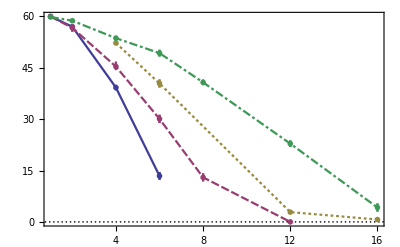

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
{{layersplot⟦j⟧,data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧},ErrorBar[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energies]}
]//.{}->Sequence[],
PlotRange->All,
Joined->True,
Background->White,
PlotTheme->{"Scientific","Monochrome"},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->10],
PlotStyle->ColorData[1]/@{1,2,3,4},
ImagePadding->{{20,5},{20,5}}
]
```

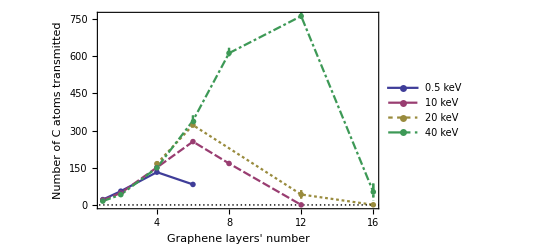

```mathematica
ejectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
{{layersplot⟦j⟧,data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energies]}
]//.{}->Sequence[],
PlotRange->All,
Joined->True,
FrameLabel->{"Graphene layers' number","Number of C atoms transmitted"},
PlotLegends->Placed[{"0.5 keV","10 keV","20 keV","40 keV"},Top],
Background->White,
PlotTheme->{"Scientific","Monochrome"},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
PlotStyle->ColorData[1]/@{1,2,3,4}
],
Epilog->Inset[inset,{1.5,800},{0,70},6]
]
```

```mathematica
Rasterize[ejectionplot,ImageResolution->600,ImageSize->2*7cm]
```

-Graphics-

```mathematica
reflection=Column[
{
"Reflection - number of C atoms",
Grid[
Join[
{Join[{""},energies]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
"---",
ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
"---",
ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energies]}
],
layers⟦j⟧
],
{j,Length[layers]}
]
],
Alignment->Left,
Spacings->{2, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Reflection - number of C atoms
 | 05keV | 10keV | 20keV | 40keV
1L | C60: | 0.00±0.00
Graph: | 0.00±0.00 | C60: | 0.00±0.00
Graph: | 0.13±0.13 | C60: | ---
Graph: | --- | C60: | 0.14±0.14
Graph: | 1.86±0.86
2L | C60: | 0.00±0.00
Graph: | 0.00±0.00 | C60: | 0.10±0.04
Graph: | 0.40±0.12 | C60: | ---
Graph: | --- | C60: | 0.00±0.00
Graph: | 3.75±0.59
4L | C60: | 0.00±0.00
Graph: | 0.12±0.12 | C60: | 0.10±0.04
Graph: | 0.61±0.17 | C60: | 0.31±0.15
Graph: | 2.06±0.38 | C60: | 0.00±0.00
Graph: | 7.75±0.77
6L | C60: | 0.58±0.29
Graph: | 0.42±0.19 | C60: | 0.17±0.11
Graph: | 1.25±0.45 | C60: | 0.07±0.07
Graph: | 4.21±0.74 | C60: | 0.29±0.18
Graph: | 8.14±2.10
8L | C60: | ---
Graph: | --- | C60: | 0.50±0.27
Graph: | 0.75±0.41 | C60: | ---
Graph: | --- | C60: | 0.13±0.13
Graph: | 13.50±2.85
12L | C60: | ---
Graph: | --- | C60: | 0.14±0.14
Graph: | 0.57±0.37 | C60: | 0.00±0.00
Graph: | 6.29±1.58 | C60: | 0.14±0.14
Graph: | 18.71±3.23
16L | C60: | ---
Graph: | --- | C60: | ---
Graph: | --- | C60: | 0.31±0.13
Graph: | 4.54±1.01 | C60: | 0.40±0.24
Graph: | 13.00±4.36

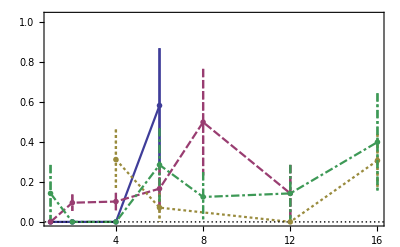

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
{{layersplot⟦j⟧,data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧},ErrorBar[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energies]}
]//.{}->Sequence[],
PlotRange->{All,{All,1.03}},
Joined->True,
Background->White,
PlotTheme->{"Scientific","Monochrome"},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->10],
PlotStyle->ColorData[1]/@{1,2,3,4},
ImagePadding->{{20,5},{20,5}}
]
```

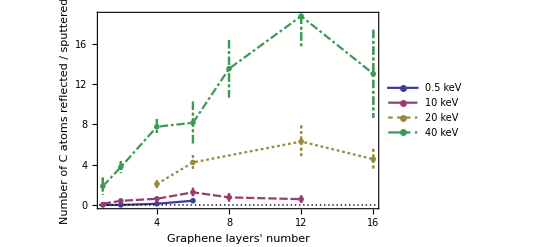

```mathematica
reflectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]],
{{layersplot⟦j⟧,data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energies⟦i⟧,layers⟦j⟧,"00deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energies]}
]//.{}->Sequence[],
PlotRange->All,
Joined->True,
FrameLabel->{"Graphene layers' number","Number of C atoms reflected / sputtered"},
PlotLegends->Placed[{"0.5 keV","10 keV","20 keV","40 keV"},Top],
Background->White,
PlotTheme->{"Scientific","Monochrome"},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
PlotStyle->ColorData[1]/@{1,2,3,4}
],
Epilog->Inset[inset,{1.5,19.5},{0,1.15},6]
]
```

```mathematica
Rasterize[reflectionplot,ImageResolution->600,ImageSize->2*7cm]
```

-Graphics-

```mathematica
energiesangleplot={10,40};
layersplot={1,2,4,6,8,12,16};
```

```mathematica
energiesangle={"10keV","40keV"};
```

```mathematica
anglesplot={0,15,30,45,50,55,60,65,70,75,77,80};
```

```mathematica
ejection=Column[
{
"Ejection - number of C atoms",
Grid[
Join[
{Join[{""},energiesangle]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energiesangle]}
],
layers⟦j⟧
],
{j,Length[layers]}
]
],
Alignment->Left,
Spacings->{2, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Ejection - number of C atoms
 | 10keV | 40keV
1L | C60: | 53.50±0.76
Graph: | 31.13±1.11 | C60: | 57.71±0.36
Graph: | 23.86±1.45
2L | C60: | 46.43±1.25
Graph: | 83.43±1.43 | C60: | 54.43±1.17
Graph: | 68.71±4.94
4L | C60: | 25.25±0.88
Graph: | 210.37±4.86 | C60: | 43.71±1.08
Graph: | 263.29±10.94
6L | C60: | 11.88±1.49
Graph: | 173.62±9.62 | C60: | ---
Graph: | ---
8L | C60: | ---
Graph: | --- | C60: | 27.25±1.19
Graph: | 744.25±15.08
12L | C60: | ---
Graph: | --- | C60: | 7.50±1.48
Graph: | 280.87±16.86
16L | C60: | ---
Graph: | --- | C60: | 1.17±0.31
Graph: | 5.83±0.95

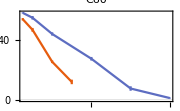

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
{{layersplot⟦j⟧,data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
ImageSize->Small,
PlotLabel->"C60"
]
```

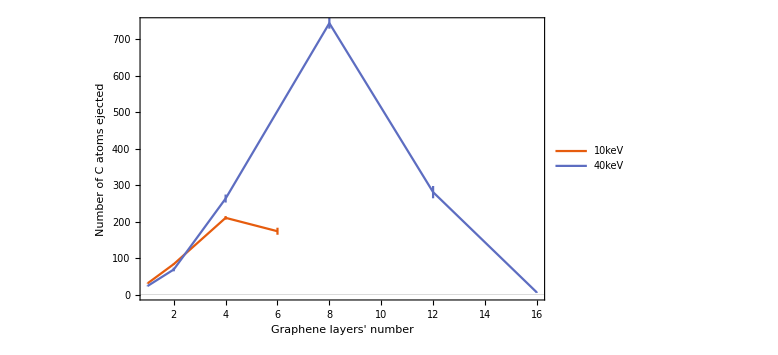

```mathematica
ejectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
{{layersplot⟦j⟧,data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
FrameLabel->{"Graphene layers' number","Number of C atoms ejected"},
PlotLegends->Placed[energiesangle,Top],
ImageSize->Large
],
Epilog->Inset[inset,Scaled[{0.2,0.75}]]
]
```

```mathematica
Rasterize[ejectionplot]
```

-Graphics-

```mathematica
reflection=Column[
{
"Reflection - number of C atoms",
Grid[
Join[
{Join[{""},energiesangle]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energiesangle]}
],
layers⟦j⟧
],
{j,Length[layers]}
]
],
Alignment->Left,
Spacings->{2, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Reflection - number of C atoms
 | 10keV | 40keV
1L | C60: | 5.13±0.79
Graph: | 11.00±1.07 | C60: | 2.14±0.34
Graph: | 13.00±1.05
2L | C60: | 5.71±0.84
Graph: | 30.86±3.61 | C60: | 3.43±0.65
Graph: | 36.71±6.73
4L | C60: | 8.25±1.08
Graph: | 53.25±6.30 | C60: | 5.00±0.76
Graph: | 116.57±11.19
6L | C60: | 9.25±0.96
Graph: | 63.25±4.26 | C60: | ---
Graph: | ---
8L | C60: | ---
Graph: | --- | C60: | 5.75±0.84
Graph: | 240.75±16.27
12L | C60: | ---
Graph: | --- | C60: | 7.00±0.76
Graph: | 286.25±33.69
16L | C60: | ---
Graph: | --- | C60: | 7.00±0.73
Graph: | 292.17±18.41

```mathematica
Rasterize[reflection]
```

-Graphics-

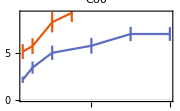

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
{{layersplot⟦j⟧,data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
ImageSize->Small,
PlotLabel->"C60"
]
```

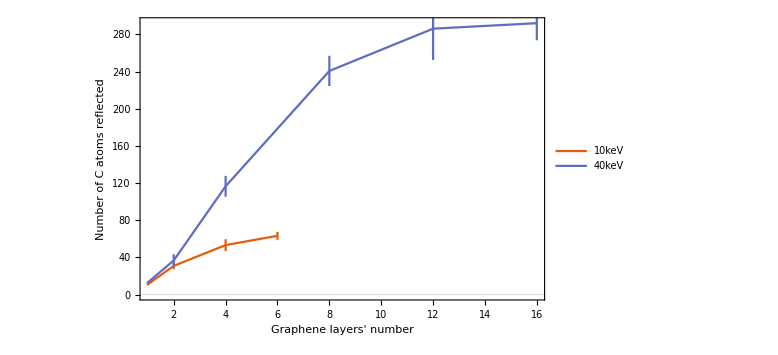

```mathematica
reflectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]],
{{layersplot⟦j⟧,data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,layers⟦j⟧,"45deg"}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[layers]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
FrameLabel->{"Graphene layers' number","Number of C atoms reflected"},
PlotLegends->Placed[energiesangle,Top],
ImageSize->Large
],
Epilog->Inset[inset,Scaled[{0.2,0.75}]]
]
```

```mathematica
Rasterize[reflectionplot]
```

-Graphics-

```mathematica
ejection=Column[
{
"Ejection - number of C atoms",
Grid[
Join[
{Join[{""},energiesangle]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energiesangle]}
],
angles⟦j⟧
],
{j,Length[angles]}
]
],
Alignment->Left,
Spacings->{1, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Ejection - number of C atoms
 | 10keV | 40keV
00deg | C60: | 56.67±1.13
Graph: | 48.17±1.22 | C60: | 58.75±0.37
Graph: | 41.50±2.15
15deg | C60: | 57.13±0.83
Graph: | 50.50±1.56 | C60: | 58.29±0.57
Graph: | 42.43±1.91
30deg | C60: | 53.63±0.65
Graph: | 65.62±2.31 | C60: | 58.00±0.58
Graph: | 58.71±4.44
45deg | C60: | 46.43±1.25
Graph: | 83.43±1.43 | C60: | 54.43±1.17
Graph: | 68.71±4.94
50deg | C60: | 37.63±1.00
Graph: | 97.62±3.84 | C60: | ---
Graph: | ---
55deg | C60: | 30.43±1.13
Graph: | 115.14±3.10 | C60: | 46.63±1.00
Graph: | 98.75±4.04
60deg | C60: | 19.00±1.00
Graph: | 124.12±3.81 | C60: | 39.13±1.79
Graph: | 122.37±5.93
65deg | C60: | 8.62±0.71
Graph: | 121.87±2.07 | C60: | 30.88±1.04
Graph: | 137.37±4.96
70deg | C60: | 3.13±0.44
Graph: | 80.87±4.51 | C60: | 17.63±0.75
Graph: | 165.50±4.26
75deg | C60: | 0.50±0.19
Graph: | 20.88±1.60 | C60: | 7.88±1.46
Graph: | 187.00±7.06
77deg | C60: | ---
Graph: | --- | C60: | 2.50±0.62
Graph: | 150.67±10.71
80deg | C60: | 1.63±0.53
Graph: | 0.00±0.00 | C60: | 0.25±0.16
Graph: | 28.63±5.53

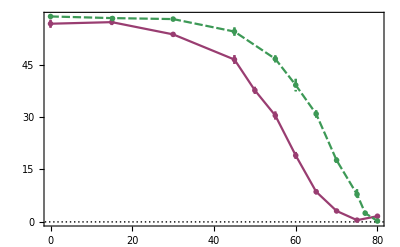

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
{{anglesplot⟦j⟧,data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧]},{}],
{j,Length[angles]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotRange->All,
Joined->True,
Background->White,
PlotTheme->{"Scientific","Monochrome"},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
PlotStyle->ColorData[1]/@{2,4},
GridLines->{None,{0}}
]
```

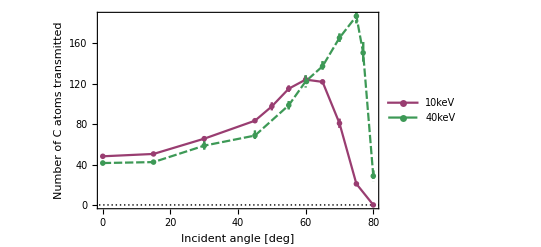

```mathematica
ejectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
{{anglesplot⟦j⟧,data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[angles]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotRange->All,
Joined->True,
FrameLabel->{"Incident angle [deg]","Number of C atoms transmitted"},
PlotLegends->Placed[energiesangle,Top],
Background->White,
PlotTheme->{"Scientific","Monochrome"},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
PlotStyle->ColorData[1]/@{2,4},
GridLines->{None,{0}}
],
Epilog->Inset[inset,{5,200},{0,70},40]
]
```

```mathematica
Rasterize[ejectionplot,ImageResolution->600,ImageSize->2*7cm]
```

-Graphics-

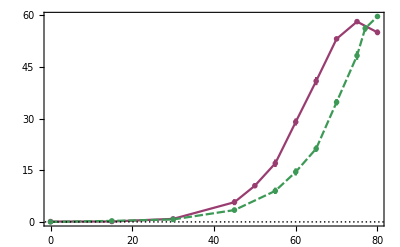

```mathematica
inset=ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
{{anglesplot⟦j⟧,data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧]},{}],
{j,Length[angles]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotRange->All,
Joined->True,
Background->White,
PlotTheme->{"Scientific","Monochrome"},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
PlotStyle->ColorData[1]/@{2,4},
GridLines->{None,{0}}
]
```

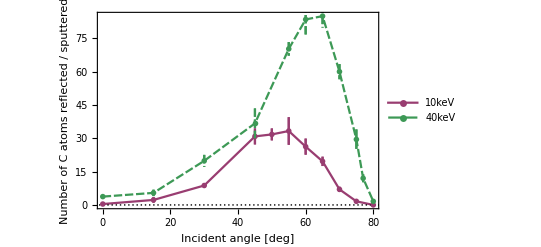

```mathematica
reflectionplot=Show[
ErrorListPlot[
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
{{anglesplot⟦j⟧,data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[angles]}
],
{i,Length[energiesangle]}
]//.{}->Sequence[],
PlotRange->All,
Joined->True,
FrameLabel->{"Incident angle [deg]","Number of C atoms reflected / sputtered"},
PlotLegends->Placed[energiesangle,Top],
Background->White,
PlotTheme->{"Scientific","Monochrome"},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
PlotStyle->ColorData[1]/@{2,4},
GridLines->{None,{0}}
],
Epilog->Inset[inset,{5,85},{0,60},40]
]
```

```mathematica
Rasterize[reflectionplot,ImageResolution->600,ImageSize->2*7cm]
```

-Graphics-

```mathematica
reflection=Column[
{
"Reflection - number of C atoms",
Grid[
Join[
{Join[{""},energiesangle]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,"2L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energiesangle]}
],
angles⟦j⟧
],
{j,Length[angles]}
]
],
Alignment->Left,
Spacings->{1, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Reflection - number of C atoms
 | 10keV | 40keV
00deg | C60: | 0.10±0.04
Graph: | 0.40±0.12 | C60: | 0.00±0.00
Graph: | 3.75±0.59
15deg | C60: | 0.13±0.13
Graph: | 2.25±1.21 | C60: | 0.29±0.18
Graph: | 5.43±1.45
30deg | C60: | 0.88±0.40
Graph: | 8.75±0.92 | C60: | 0.71±0.47
Graph: | 19.86±2.69
45deg | C60: | 5.71±0.84
Graph: | 30.86±3.61 | C60: | 3.43±0.65
Graph: | 36.71±6.73
50deg | C60: | 10.50±0.60
Graph: | 31.75±2.68 | C60: | ---
Graph: | ---
55deg | C60: | 17.00±1.07
Graph: | 33.29±6.22 | C60: | 9.00±0.91
Graph: | 70.25±3.06
60deg | C60: | 29.00±0.98
Graph: | 26.25±3.63 | C60: | 14.50±0.98
Graph: | 83.50±7.00
65deg | C60: | 40.88±1.17
Graph: | 19.63±2.10 | C60: | 21.25±0.88
Graph: | 85.00±5.15
70deg | C60: | 53.13±0.52
Graph: | 7.00±1.16 | C60: | 34.75±0.90
Graph: | 60.00±3.41
75deg | C60: | 58.13±0.64
Graph: | 1.63±0.60 | C60: | 48.25±1.24
Graph: | 29.50±4.49
77deg | C60: | ---
Graph: | --- | C60: | 56.17±0.91
Graph: | 12.00±1.77
80deg | C60: | 55.00±0.78
Graph: | 0.00±0.00 | C60: | 59.62±0.18
Graph: | 1.63±0.60

```mathematica
ejection=Column[
{
"Ejection - number of C atoms",
Grid[
Join[
{Join[{""},energiesangle]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energiesangle]}
],
angles⟦j⟧
],
{j,Length[angles]}
]
],
Alignment->Left,
Spacings->{1, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Ejection - number of C atoms
 | 10keV | 40keV
00deg | C60: | 13.00±1.16
Graph: | 167.25±6.68 | C60: | 40.75±0.82
Graph: | 612.13±21.38
15deg | C60: | ---
Graph: | --- | C60: | 39.67±1.33
Graph: | 586.17±32.41
30deg | C60: | ---
Graph: | --- | C60: | 35.57±0.97
Graph: | 670.71±18.89
45deg | C60: | ---
Graph: | --- | C60: | 27.25±1.19
Graph: | 744.25±15.08
50deg | C60: | ---
Graph: | --- | C60: | ---
Graph: | ---
55deg | C60: | ---
Graph: | --- | C60: | ---
Graph: | ---
60deg | C60: | ---
Graph: | --- | C60: | 10.75±0.80
Graph: | 506.63±14.62
65deg | C60: | ---
Graph: | --- | C60: | ---
Graph: | ---
70deg | C60: | ---
Graph: | --- | C60: | 1.33±0.42
Graph: | 51.83±14.78
75deg | C60: | ---
Graph: | --- | C60: | ---
Graph: | ---
77deg | C60: | ---
Graph: | --- | C60: | ---
Graph: | ---
80deg | C60: | ---
Graph: | --- | C60: | ---
Graph: | ---

```mathematica
inset=ErrorListPlot[
Join[
{{{}}},
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]],
{{anglesplot⟦j⟧,data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["C60"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["C60"]⟦2⟧]},{}],
{j,Length[angles]}
],
{i,{2}}
]//.{}->Sequence[]
],
PlotRange->{{All,82},{All,63}},
Joined->True,
Background->White,
PlotTheme->{"Scientific","Monochrome"},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
PlotStyle->ColorData[1]/@{2,4},
GridLines->{None,{0}}
]
```

-Graphics-

```mathematica
ejectionplot=Show[
ErrorListPlot[
Join[
{{{}}},
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]],
{{anglesplot⟦j⟧,data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["topnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[angles]}
],
{i,{2}}
]//.{}->Sequence[]
],
PlotRange->{{All,82},All},
Joined->True,
FrameLabel->{"Incident angle [deg]","Number of C atoms transmitted"},
PlotLegends->Placed[energiesangle,Top],
Background->White,
PlotTheme->{"Scientific","Monochrome"},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
PlotStyle->ColorData[1]/@{2,4},
GridLines->{None,{0}}
],
Epilog->Inset[inset,{5,100},{0,0},40]
]
```

-Graphics-

```mathematica
Rasterize[ejectionplot,ImageResolution->600,ImageSize->2*7cm]
```

-Graphics-

```mathematica
inset=ErrorListPlot[
Join[
{{{}}},
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]],
{{anglesplot⟦j⟧,data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧]},{}],
{j,Length[angles]}
],
{i,{2}}
]//.{}->Sequence[]
],
PlotRange->{{All,82},{All,63}},
Joined->True,
Background->White,
PlotTheme->{"Scientific","Monochrome"},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
PlotStyle->ColorData[1]/@{2,4},
GridLines->{None,{0}}
]
```

-Graphics-

```mathematica
reflectionplot=Show[
ErrorListPlot[
Join[
{{{}}},
Table[
Table[
If[!MissingQ[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]],
{{anglesplot⟦j⟧,data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧},ErrorBar[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧]},{}],
{j,Length[angles]}
],
{i,{2}}
]//.{}->Sequence[]
],
PlotRange->{{All,82},All},
Joined->True,
FrameLabel->{"Incident angle [deg]","Number of C atoms reflected / sputtered"},
PlotLegends->Placed[energiesangle,Top],
Background->White,
PlotTheme->{"Scientific","Monochrome"},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
PlotStyle->ColorData[1]/@{2,4},
GridLines->{None,{0}}
],
Epilog->Inset[inset,{5,365},{0,60},40]
]
```

-Graphics-

```mathematica
Rasterize[reflectionplot,ImageResolution->600,ImageSize->2*7cm]
```

-Graphics-

```mathematica
reflection=Column[
{
"Reflection - number of C atoms",
Grid[
Join[
{Join[{""},energiesangle]},
Table[
Prepend[
Table[
Grid[
{
{
"C60:",
If[MissingQ[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["C60"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["C60"]⟦2⟧,{Infinity,2}]]
]
},
{
"Graph:",
If[MissingQ[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]],
"---",
ToString[NumberForm[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["Graph"]⟦1⟧,{Infinity,2}]]<>"±"<>ToString[NumberForm[data[{energiesangle⟦i⟧,"8L",angles⟦j⟧}]["results"]["yield"]["bottomnumber"]["Graph"]⟦2⟧,{Infinity,2}]]
]
}
},
Alignment->{{Right,"±"}}
],
{i,Length[energiesangle]}
],
angles⟦j⟧
],
{j,Length[angles]}
]
],
Alignment->Left,
Spacings->{1, 1},
Dividers->{2->True,2->True}
]
},
Alignment->Center
]
```

Reflection - number of C atoms
 | 10keV | 40keV
00deg | C60: | 0.50±0.27
Graph: | 0.75±0.41 | C60: | 0.13±0.13
Graph: | 13.50±2.85
15deg | C60: | ---
Graph: | --- | C60: | 0.00±0.00
Graph: | 22.83±3.75
30deg | C60: | ---
Graph: | --- | C60: | 1.43±0.69
Graph: | 88.29±9.96
45deg | C60: | ---
Graph: | --- | C60: | 5.75±0.84
Graph: | 240.75±16.27
50deg | C60: | ---
Graph: | --- | C60: | ---
Graph: | ---
55deg | C60: | ---
Graph: | --- | C60: | ---
Graph: | ---
60deg | C60: | ---
Graph: | --- | C60: | 16.38±1.05
Graph: | 363.75±13.42
65deg | C60: | ---
Graph: | --- | C60: | ---
Graph: | ---
70deg | C60: | ---
Graph: | --- | C60: | 33.83±1.42
Graph: | 245.67±9.24
75deg | C60: | ---
Graph: | --- | C60: | ---
Graph: | ---
77deg | C60: | ---
Graph: | --- | C60: | ---
Graph: | ---
80deg | C60: | ---
Graph: | --- | C60: | ---
Graph: | ---

#### Plot mass spectra

```mathematica
massspectrumPlotTheme={
PlotTheme->"Scientific",
(*PlotRange->All,*)
(*Filling->Bottom,*)
FillingStyle->Opacity[1],
PlotStyle->PointSize[Tiny],
FrameLabel->{"Mass",(*"Relative abundace [a.u.]"*)None}
};
```

```mathematica
move[i_]:=(i-1)*1.2;
```

```mathematica
energiessweep
```

{{{05keV,1L,00deg},{10keV,1L,00deg},{40keV,1L,00deg}},{{05keV,2L,00deg},{10keV,2L,00deg},{40keV,2L,00deg}},{{05keV,4L,00deg},{10keV,4L,00deg},{20keV,4L,00deg},{40keV,4L,00deg}},{{05keV,6L,00deg},{10keV,6L,00deg},{20keV,6L,00deg},{40keV,6L,00deg}},{{10keV,8L,00deg},{40keV,8L,00deg}},{{10keV,12L,00deg},{20keV,12L,00deg},{40keV,12L,00deg}},{{20keV,16L,00deg},{40keV,16L,00deg}}}

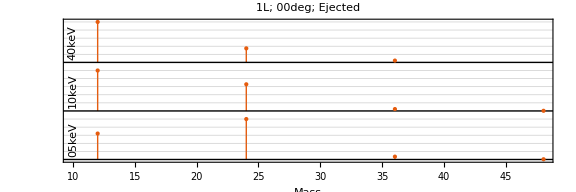
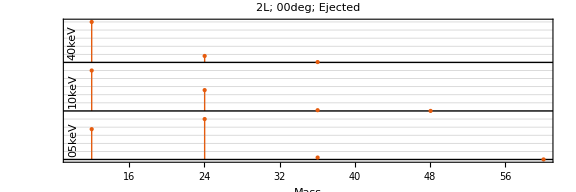
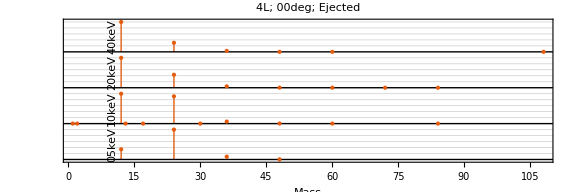
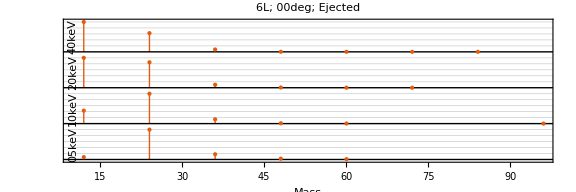
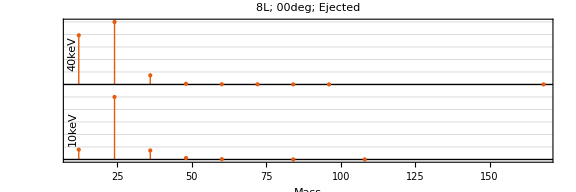
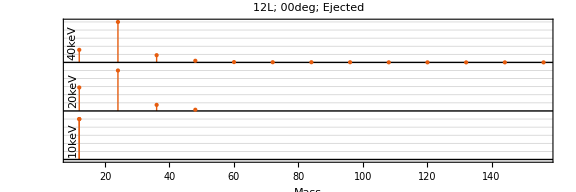
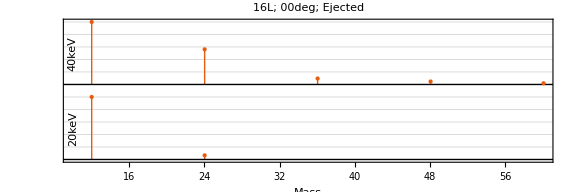

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[energiessweep⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,1⟧,data[energiessweep⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[energiessweep⟦j,i,1⟧,{10,move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[energiessweep⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{energiessweep⟦j,1,2;;3⟧,{"Ejected"}}],"; "]],
ImageSize->Large
],
{j,Length[energiessweep]}]
```

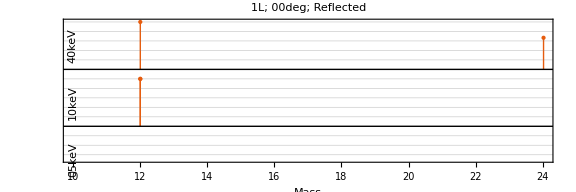
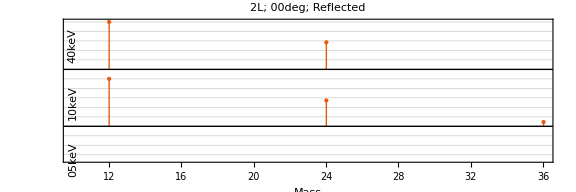
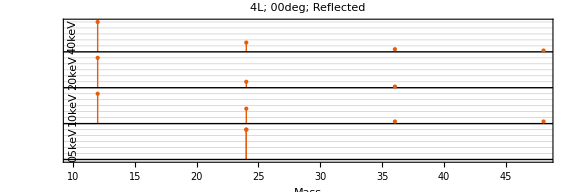
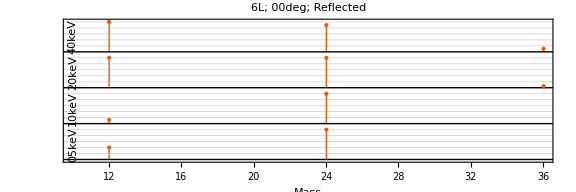
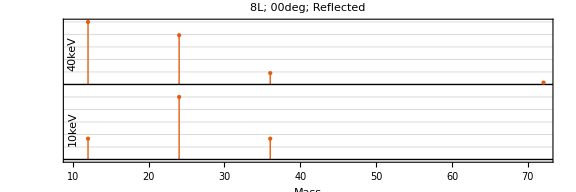
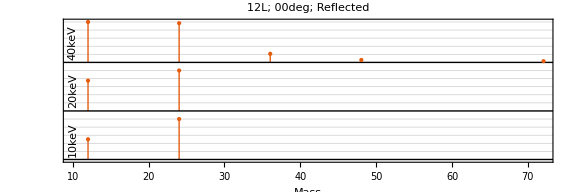
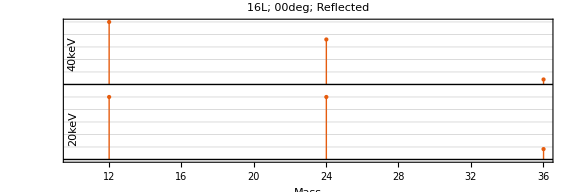

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[energiessweep⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,1⟧,data[energiessweep⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[energiessweep⟦j,i,1⟧,{10,move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[energiessweep⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{energiessweep⟦j,1,2;;3⟧,{"Reflected"}}],"; "]],
ImageSize->Large
],
{j,Length[energiessweep]}]
```

```mathematica
layerssweep
```

{{{05keV,1L,00deg},{05keV,2L,00deg},{05keV,4L,00deg},{05keV,6L,00deg}},{{10keV,1L,00deg},{10keV,2L,00deg},{10keV,4L,00deg},{10keV,6L,00deg},{10keV,8L,00deg},{10keV,12L,00deg}},{{20keV,4L,00deg},{20keV,6L,00deg},{20keV,12L,00deg},{20keV,16L,00deg}},{{40keV,1L,00deg},{40keV,2L,00deg},{40keV,4L,00deg},{40keV,6L,00deg},{40keV,8L,00deg},{40keV,12L,00deg},{40keV,16L,00deg}}}

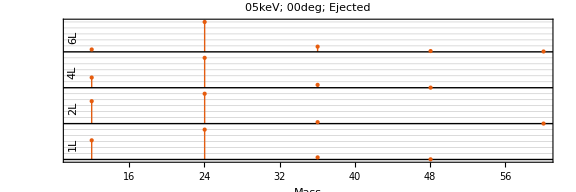
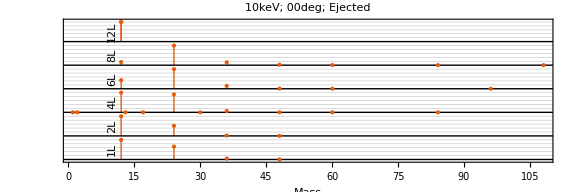
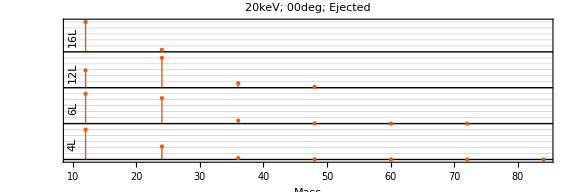
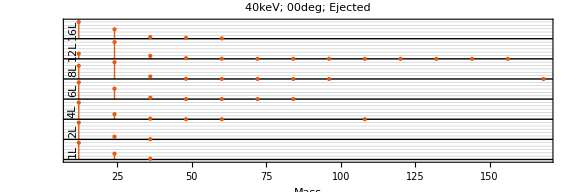

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[layerssweep⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,1⟧,data[layerssweep⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[layerssweep⟦j,i,2⟧,{10,move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[layerssweep⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{layerssweep⟦j,1,{1,3}⟧,{"Ejected"}}],"; "]],
ImageSize->Large
],
{j,Length[layerssweep]}]
```

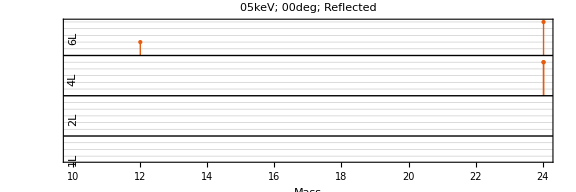
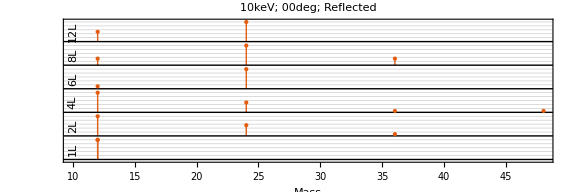
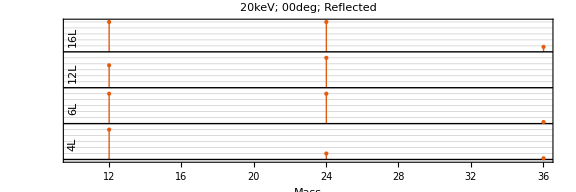
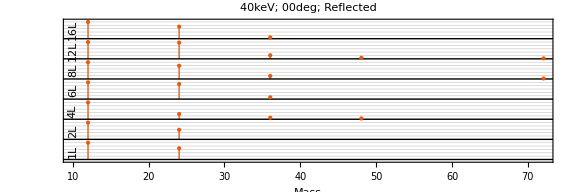

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[layerssweep⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,1⟧,data[layerssweep⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[layerssweep⟦j,i,2⟧,{10,move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[layerssweep⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{layerssweep⟦j,1,{1,3}⟧,{"Reflected"}}],"; "]],
ImageSize->Large
],
{j,Length[layerssweep]}]
```

```mathematica
layerssweep45
```

{{{10keV,1L,45deg},{10keV,2L,45deg},{10keV,4L,45deg},{10keV,6L,45deg}},{{40keV,1L,45deg},{40keV,2L,45deg},{40keV,4L,45deg},{40keV,8L,45deg},{40keV,12L,45deg},{40keV,16L,45deg}}}

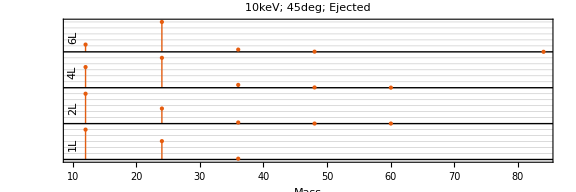
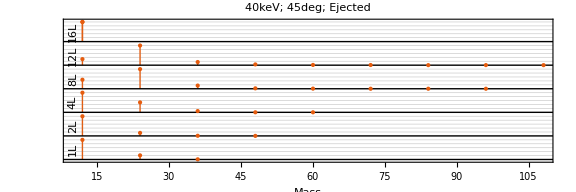

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[layerssweep45⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,1⟧,data[layerssweep45⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[layerssweep45⟦j,i,2⟧,{10,move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[layerssweep45⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{layerssweep45⟦j,1,{1,3}⟧,{"Ejected"}}],"; "]],
ImageSize->Large
],
{j,Length[layerssweep45]}]
```

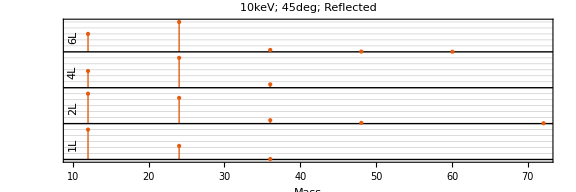
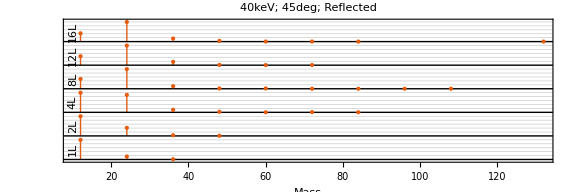

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[layerssweep45⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,1⟧,data[layerssweep45⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[layerssweep45⟦j,i,2⟧,{10,move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[layerssweep45⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{layerssweep45⟦j,1,{1,3}⟧,{"Reflected"}}],"; "]],
ImageSize->Large
],
{j,Length[layerssweep45]}]
```

```mathematica
anglessweep
```

{{{10keV,2L,00deg},{10keV,2L,15deg},{10keV,2L,30deg},{10keV,2L,45deg},{10keV,2L,50deg},{10keV,2L,55deg},{10keV,2L,60deg},{10keV,2L,65deg},{10keV,2L,70deg},{10keV,2L,75deg},{10keV,2L,80deg}},{{40keV,2L,00deg},{40keV,2L,15deg},{40keV,2L,30deg},{40keV,2L,45deg},{40keV,2L,55deg},{40keV,2L,60deg},{40keV,2L,65deg},{40keV,2L,70deg},{40keV,2L,75deg},{40keV,2L,77deg},{40keV,2L,80deg}}}

```mathematica
move[i_]:=(i-1)*1.2;
```

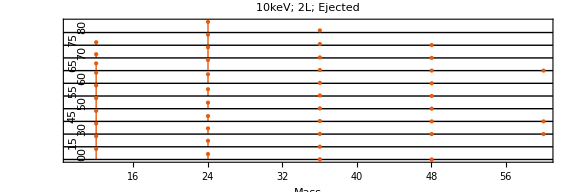
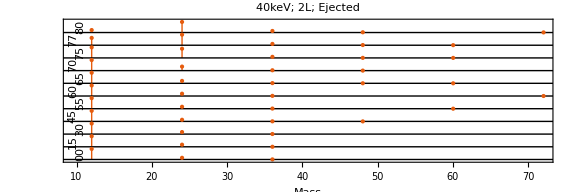

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[anglessweep⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,1⟧,data[anglessweep⟦j,i⟧]["results"]["massspectrum"]["toprelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[StringTake[anglessweep⟦j,i,3⟧,2],{10-If[EvenQ[i],0.5,-0.5],move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[anglessweep⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{anglessweep⟦j,1,{1,2}⟧,{"Ejected"}}],"; "]],
ImageSize->Large
],
{j,Length[anglessweep]}]
```

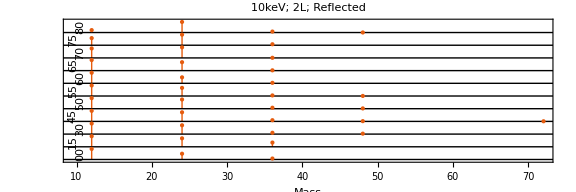
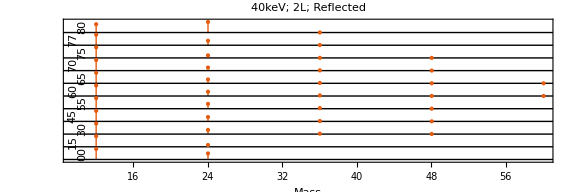

```mathematica
Table[
aaa=Table[
Show[
{
ListPlot[
Transpose[{data[anglessweep⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,1⟧,data[anglessweep⟦j,i⟧]["results"]["massspectrum"]["bottomrelative"]⟦;;,2⟧+move[i]}],
massspectrumPlotTheme,
Filling->move[i],
PlotRange->{All,{move[i],All}}
],
Graphics[{Thin,InfiniteLine[{{0,move[i]},{50,move[i]}}]}],
Graphics[Text[StringTake[anglessweep⟦j,i,3⟧,2],{10-If[EvenQ[i],0.5,-0.5],move[i]+0.5},{0,0},{0,1},Background->White]]
}
],
{i,Length[anglessweep⟦j⟧]}
];

Show[
aaa,
PlotRange->All,
GridLines->{None,Flatten[Table[Range[move[i]+0.2,move[i]+1,0.2],{i,1,Length[aaa],1}]]},
FrameTicks->{Automatic,None},
AspectRatio->1/3,
PlotLabel->StringJoin[Riffle[Flatten[{anglessweep⟦j,1,{1,2}⟧,{"Reflected"}}],"; "]],
ImageSize->Large
],
{j,Length[anglessweep]}]
```

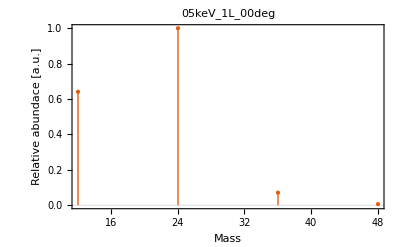
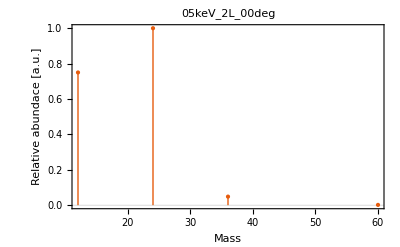
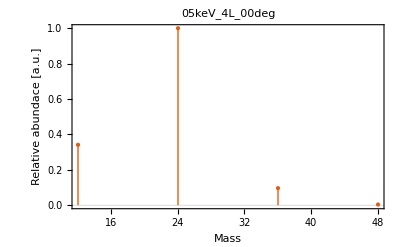
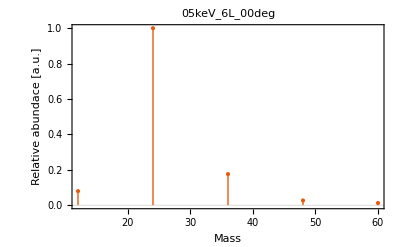
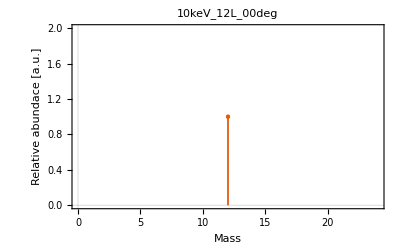
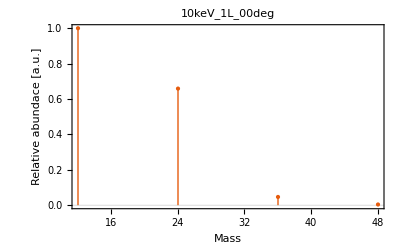
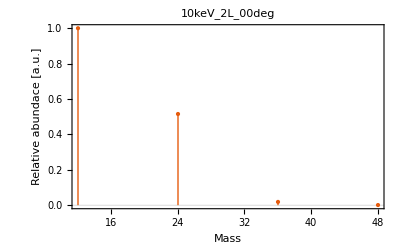
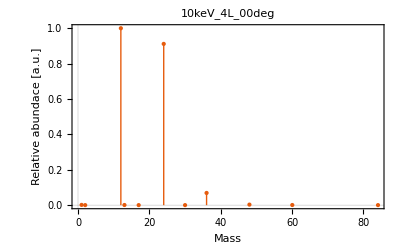

```mathematica
Table[
ListPlot[
data[datakeys⟦i⟧]["results"]["massspectrum"]["toprelative"],
massspectrumPlotTheme,
PlotLabel->StringJoin[Riffle[datakeys⟦i⟧,"_"]]
],
{i,Length[datakeys]}
]
```

#### Plot angular distributions

```mathematica
Transpose[{Range[Length[datakeys]],datakeys}]
```

{{1,{05keV,12L,00deg}},{2,{05keV,16L,00deg}},{3,{05keV,1L,00deg}},{4,{05keV,2L,00deg}},{5,{05keV,4L,00deg}},{6,{05keV,6L,00deg}},{7,{05keV,8L,00deg}},{8,{10keV,12L,00deg}},{9,{10keV,12L,45deg}},{10,{10keV,16L,00deg}},{11,{10keV,16L,45deg}},{12,{10keV,1L,00deg}},{13,{10keV,1L,45deg}},{14,{10keV,2L,00deg}},{15,{10keV,2L,15deg}},{16,{10keV,2L,30deg}},{17,{10keV,2L,45deg}},{18,{10keV,2L,50deg}},{19,{10keV,2L,55deg}},{20,{10keV,2L,60deg}},{21,{10keV,2L,65deg}},{22,{10keV,2L,70deg}},{23,{10keV,2L,75deg}},{24,{10keV,2L,80deg}},{25,{10keV,4L,00deg}},{26,{10keV,4L,45deg}},{27,{10keV,6L,00deg}},{28,{10keV,6L,45deg}},{29,{10keV,8L,00deg}},{30,{10keV,8L,45deg}},{31,{20keV,12L,00deg}},{32,{20keV,16L,00deg}},{33,{20keV,1L,00deg}},{34,{20keV,2L,00deg}},{35,{20keV,4L,00deg}},{36,{20keV,6L,00deg}},{37,{20keV,8L,00deg}},{38,{40keV,12L,00deg}},{39,{40keV,12L,45deg}},{40,{40keV,16L,00deg}},{41,{40keV,16L,45deg}},{42,{40keV,16L,60deg}},{43,{40keV,1L,00deg}},{44,{40keV,1L,45deg}},{45,{40keV,2L,00deg}},{46,{40keV,2L,15deg}},{47,{40keV,2L,30deg}},{48,{40keV,2L,45deg}},{49,{40keV,2L,55deg}},{50,{40keV,2L,60deg}},{51,{40keV,2L,65deg}},{52,{40keV,2L,70deg}},{53,{40keV,2L,75deg}},{54,{40keV,2L,77deg}},{55,{40keV,2L,80deg}},{56,{40keV,4L,00deg}},{57,{40keV,4L,45deg}},{58,{40keV,6L,00deg}},{59,{40keV,6L,45deg}},{60,{40keV,8L,00deg}},{61,{40keV,8L,15deg}},{62,{40keV,8L,30deg}},{63,{40keV,8L,45deg}},{64,{40keV,8L,60deg}},{65,{40keV,8L,70deg}}}

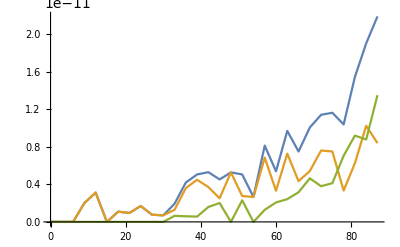

```mathematica
ListLinePlot[{data[datakeys⟦48⟧]["results"]["angledist"]["top"]["all"],data[datakeys⟦48⟧]["results"]["angledist"]["graph"]["all"],data[datakeys⟦48⟧]["results"]["angledist"]["c60"]["all"]}]
```

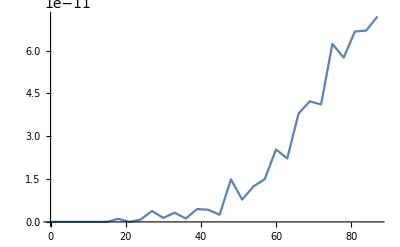

```mathematica
ListLinePlot[Transpose[{data[datakeys⟦48⟧]["results"]["angledist"]["c60"]["all"]⟦;;,1⟧,MovingAverage[data[datakeys⟦48⟧]["results"]["angledist"]["c60"]["all"]⟦;;,2⟧,2]}]]
```

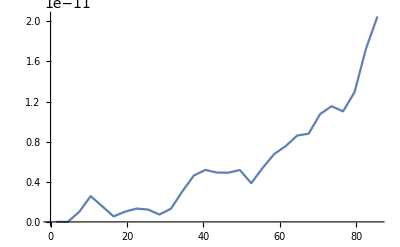

```mathematica
ListLinePlot[MovingAverage[data[datakeys⟦48⟧]["results"]["angledist"]["top"]["all"],2]]
```

```mathematica
angledistPlotTheme={
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,  
FrameLabel->{"Angle [deg]","Relative abundace [a.u.]"}
};
```

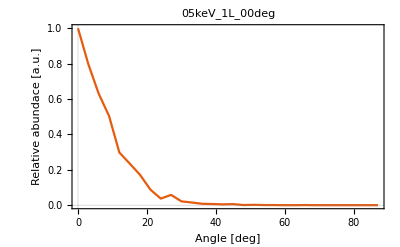
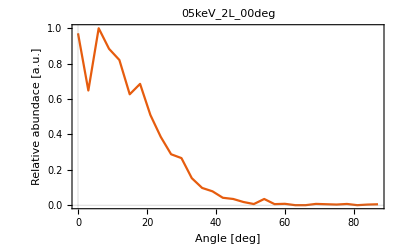
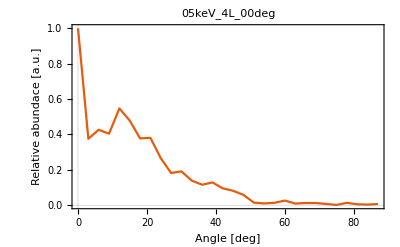
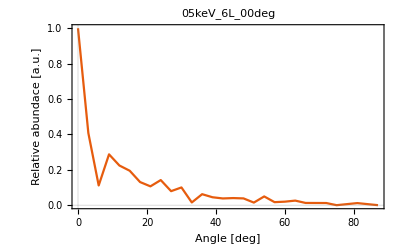
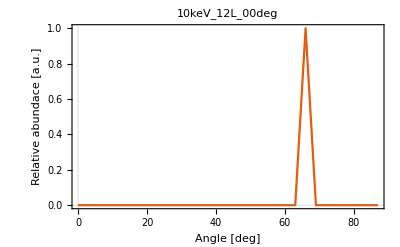
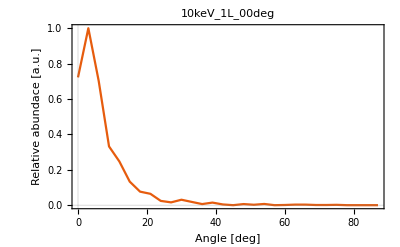
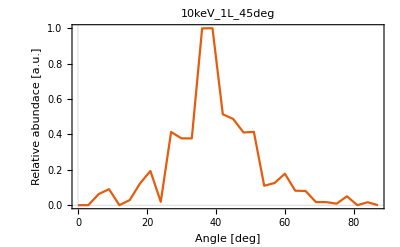
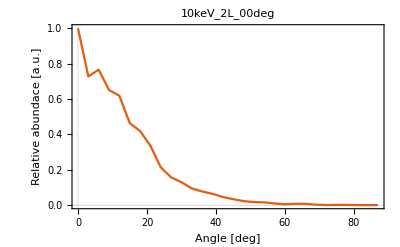
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
ListPlot[
data[datakeys⟦i⟧]["results"]["angledist"]["c60relative"]["all"],
angledistPlotTheme,
PlotLabel->StringJoin[Riffle[datakeys⟦i⟧,"_"]]
],
{i,Length[datakeys]}
]
```

```mathematica
ejectionangleplot1=ListPlot[
Table[
If[!MissingQ[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]],
Transpose[{MovingAverage[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]["results"]["angledist"]["toprelative"]["all"],2]⟦;;,1⟧,MovingAverage[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]["results"]["angledist"]["toprelative"]["all"],2]⟦;;,2⟧/Max[MovingAverage[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]["results"]["angledist"]["toprelative"]["all"],2]⟦;;,2⟧]}],{}],
{j,Length[{"00deg","15deg","30deg","45deg"}]}
]//.{}->Sequence[],
Joined->True,
PlotRange->All,
PlotTheme->{"Scientific","Monochrome"},
PlotLegends->Placed[{"00deg","15deg","30deg","45deg"},{Right,Top}],
PlotStyle->ColorData[23]/@({1,2,3,4}),
AspectRatio->1,
Background->White,
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
GridLines->{None,{0}},
FrameLabel->{"Azimuthal ejection angle [deg]","Normalized number of atoms transmitted [a.u.]"}
]
```

-Graphics-

```mathematica
Export["tmp.txt",Transpose[Table[
If[!MissingQ[data[{"40keV","8L",{"00deg","15deg","30deg","45deg","60deg","70deg"}⟦j⟧}]],
data[{"40keV","8L",{"00deg","15deg","30deg","45deg","60deg","70deg"}⟦j⟧}]["results"]["angledist"]["c60relative"]["all"],{}],
{j,Length[{"00deg","15deg","30deg","45deg","60deg","70deg"}]}
]⟦;;,;;,2⟧],"TSV"]
```

tmp.txt

```mathematica
Export["tmp.txt",Transpose[Table[
If[!MissingQ[data[{"40keV","2L",{"00deg","15deg","30deg","45deg","60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]],
data[{"40keV","2L",{"00deg","15deg","30deg","45deg","60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]["results"]["angledist"]["c60"]["all"],{}],
{j,Length[{"00deg","15deg","30deg","45deg","60deg","70deg","75deg","77deg","80deg"}]}
]⟦;;,;;,2⟧],"TSV"]
```

tmp.txt

```mathematica
StringRiffle[ToString/@Table[
If[!MissingQ[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]],
Transpose[{MovingAverage[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]["results"]["angledist"]["c60relative"]["all"],2]⟦;;,1⟧,MovingAverage[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]["results"]["angledist"]["c60relative"]["all"],2]⟦;;,2⟧/Max[MovingAverage[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]["results"]["angledist"]["c60relative"]["all"],2]⟦;;,2⟧]}],{}],
{j,Length[{"00deg","15deg","30deg","45deg"}]}
]⟦4,;;,2⟧,"\n"]
```

0.316453
0.126929
0.399667
0.592102
0.465197
0.344362
0.458287
0.432934
0.381503
0.477848
0.576649
0.742571
0.881871
1.
0.998951
0.935605
0.74082
0.411421
0.296841
0.230277
0.176861
0.154331
0.115669
0.104416
0.0604769
0.
0.
0.0166188
0.0249054

```mathematica
StringRiffle[ToString/@Table[
If[!MissingQ[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]],
Transpose[{MovingAverage[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]["results"]["angledist"]["c60relative"]["all"],2]⟦;;,1⟧,MovingAverage[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]["results"]["angledist"]["c60relative"]["all"],2]⟦;;,2⟧/Max[MovingAverage[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]["results"]["angledist"]["c60relative"]["all"],2]⟦;;,2⟧]}],{}],
{j,Length[{"60deg","70deg","75deg","77deg","80deg"}]}
]⟦5,;;,2⟧,"\n"]
```

0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
1.
1.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.793625

```mathematica
ListPlot[
Table[
If[!MissingQ[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]],
Transpose[{MovingAverage[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]["results"]["angledist"]["graphrelative"]["all"],2]⟦;;,1⟧,MovingAverage[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]["results"]["angledist"]["graphrelative"]["all"],2]⟦;;,2⟧/Max[MovingAverage[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]["results"]["angledist"]["graphrelative"]["all"],2]⟦;;,2⟧]}],{}],
{j,Length[{"00deg","15deg","30deg","45deg"}]}
]//.{}->Sequence[],
Joined->True,
PlotRange->All,
PlotTheme->{"Scientific","Monochrome"},
PlotLegends->Placed[{"00deg","15deg","30deg","45deg"},{Right,Top}],
PlotStyle->ColorData[23]/@({1,2,3,4}),
AspectRatio->1,
Background->White,
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
GridLines->{None,{0}},
FrameLabel->{"Azimuthal ejection angle [deg]","Normalized number of atoms transmitted [a.u.]"}
]
```

-Graphics-

```mathematica
ListPlot[
Table[
If[!MissingQ[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]],
Transpose[{MovingAverage[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]["results"]["angledist"]["c60relative"]["all"],2]⟦;;,1⟧,MovingAverage[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]["results"]["angledist"]["c60relative"]["all"],2]⟦;;,2⟧/Max[MovingAverage[data[{"40keV","2L",{"00deg","15deg","30deg","45deg"}⟦j⟧}]["results"]["angledist"]["c60relative"]["all"],2]⟦;;,2⟧]}],{}],
{j,Length[{"00deg","15deg","30deg","45deg"}]}
]//.{}->Sequence[],
Joined->True,
PlotRange->All,
PlotTheme->{"Scientific","Monochrome"},
PlotLegends->Placed[{"00deg","15deg","30deg","45deg"},{Right,Top}],
PlotStyle->ColorData[23]/@({1,2,3,4}),
AspectRatio->1,
Background->White,
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
GridLines->{None,{0}},
FrameLabel->{"Azimuthal ejection angle [deg]","Normalized number of atoms transmitted [a.u.]"}
]
```

-Graphics-

```mathematica
Rasterize[ejectionangleplot1,ImageResolution->600,ImageSize->2*4cm]
```

-Graphics-

```mathematica
ejectionangleplot2=ListPlot[
Table[
If[!MissingQ[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]],
Transpose[{MovingAverage[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]["results"]["angledist"]["toprelative"]["all"],2]⟦;;,1⟧,MovingAverage[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]["results"]["angledist"]["toprelative"]["all"],2]⟦;;,2⟧/Max[MovingAverage[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]["results"]["angledist"]["toprelative"]["all"],2]⟦;;,2⟧]}],{}],
{j,Length[{"60deg","70deg","75deg","77deg","80deg"}]}
]//.{}->Sequence[],
Joined->True,
PlotRange->All,
PlotTheme->{"Scientific","Monochrome"},
PlotLegends->Placed[{"60deg","70deg","75deg","77deg","80deg"},{Right,Top}],
PlotStyle->ColorData[23]/@(Range[Length[{"60deg","70deg","75deg","77deg","80deg"}]]),
AspectRatio->1,
Background->White,
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
GridLines->{None,{0}},
FrameLabel->{"Azimuthal ejection angle [deg]","Normalized number of atoms transmitted [a.u.]"}
]
```

-Graphics-

```mathematica
ListPlot[
Table[
If[!MissingQ[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]],
Transpose[{MovingAverage[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]["results"]["angledist"]["graphrelative"]["all"],2]⟦;;,1⟧,MovingAverage[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]["results"]["angledist"]["graphrelative"]["all"],2]⟦;;,2⟧/Max[MovingAverage[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]["results"]["angledist"]["graphrelative"]["all"],2]⟦;;,2⟧]}],{}],
{j,Length[{"60deg","70deg","75deg","77deg","80deg"}]}
]//.{}->Sequence[],
Joined->True,
PlotRange->All,
PlotTheme->{"Scientific","Monochrome"},
PlotLegends->Placed[{"60deg","70deg","75deg","77deg","80deg"},{Right,Top}],
PlotStyle->ColorData[23]/@(Range[Length[{"60deg","70deg","75deg","77deg","80deg"}]]),
AspectRatio->1,
Background->White,
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
GridLines->{None,{0}},
FrameLabel->{"Azimuthal ejection angle [deg]","Normalized number of atoms transmitted [a.u.]"}
]
```

-Graphics-

```mathematica
ListPlot[
Table[
If[!MissingQ[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]],
Transpose[{MovingAverage[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]["results"]["angledist"]["c60relative"]["all"],2]⟦;;,1⟧,MovingAverage[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]["results"]["angledist"]["c60relative"]["all"],2]⟦;;,2⟧/Max[MovingAverage[data[{"40keV","2L",{"60deg","70deg","75deg","77deg","80deg"}⟦j⟧}]["results"]["angledist"]["c60relative"]["all"],2]⟦;;,2⟧]}],{}],
{j,Length[{"60deg","70deg","75deg","77deg","80deg"}]}
]//.{}->Sequence[],
Joined->True,
PlotRange->All,
PlotTheme->{"Scientific","Monochrome"},
PlotLegends->Placed[{"60deg","70deg","75deg","77deg","80deg"},{Right,Top}],
PlotStyle->ColorData[23]/@(Range[Length[{"60deg","70deg","75deg","77deg","80deg"}]]),
AspectRatio->1,
Background->White,
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->12],
GridLines->{None,{0}},
FrameLabel->{"Azimuthal ejection angle [deg]","Normalized number of atoms transmitted [a.u.]"}
]
```

-Graphics-

```mathematica
Rasterize[ejectionangleplot2,ImageResolution->600,ImageSize->2*4cm]
```

-Graphics-

#### Plot energy distributions

```mathematica
data[datakeys⟦1⟧]["results"]["energies"]["top"]["total"]
```

{39.7736,174.44,31.4125,151.316,184.376,190.025,199.403,168.987,68.5862,111.294,70.5602,131.325,96.3019,79.6638,16.9826,235.883,147.113,52.2798,121.882,48.3793,46.6962,45.1155,172.287,91.2512,98.5769,52.0412,51.2819,167.903,45.691,143.69,53.1082,67.0346,108.358,26.2156,99.7922,44.625,111.829,93.6918,38.5259,85.6637,43.0845,76.7739,37.4818,16.7916,115.587,63.7801,92.6892,18.0947,159.273,19.9282,156.468,84.8532,108.39,96.137,72.2105,151.772,185.334,63.2039,120.9,141.145,6.54798,88.6912,48.0154,52.9137,149.27,40.8352,109.386,6.24425,58.6151,60.3918,57.3541,175.439,117.65,65.3865,143.742,100.866,103.452,160.806,129.697,152.476,95.5726,72.4002,63.2471,111.007,61.5492,44.6607,96.6301,115.21,93.358,69.8239,75.9333,97.0425,73.4494,34.0988,139.01,65.8199,76.9803,165.004,130.116,161.444,140.132,87.9342,24.9393,107.725,67.7382,150.663,93.6874,65.9987,44.259,112.272,185.563,77.8369,137.305,137.252,132.838,102.706,121.736,125.844,48.1952,57.633,76.5361,77.9685,72.0877,118.491,132.589,126.847,110.811,106.542,35.7885,23.0708,49.6013,87.4819,24.4388,68.0632,109.011,56.2237,113.025,96.2388,52.5133,20.2549,13.3574,20.7051,153.467,49.2982,29.6452,69.3585,175.902,115.456,112.51,141.841,20.098,56.6748,159.326,10.3027,37.825,26.2213,152.017,66.6447,240.3,114.386,112.349,59.7828,146.307,69.0905,105.114,77.3166,71.6972,207.635,34.953,119.387,68.1351,5.64118,10.2375,66.7382,104.576,111.643,87.9287,90.471,79.9703,106.24,134.286,94.6075,112.059,82.097,109.957,42.3341,100.1,58.2591,41.0412,78.6596,9.09003,99.849,57.8528,168.872,87.9688,84.8661,31.4607,105.861,74.313,94.6972,69.1461,152.906,34.7096,20.1004,37.5205,18.8431,188.958,98.8675,63.8301,108.323,149.484,72.5201,114.451,109.721,56.558,139.808,142.957,140.469,27.1087,88.0014,82.8267,150.112,194.29,55.6232,83.2666,117.719,74.8069,110.159,74.7033,111.304,36.7422,45.9555,140.583,95.449,148.005,109.767,56.0793,57.1977,24.0229,38.0822,155.942,50.8862,192.884,94.4514,40.2282,53.6021,32.7455,11.9741,11.0834,55.7399,64.7858,179.524,118.402,29.2993,126.852,73.9266,41.1137,61.5618,83.8264,44.4724,103.668,58.0375,101.565,80.3011,31.0535,70.4683,73.157,116.432,158.621,8.775,92.2853,148.155,118.98,21.0316,68.2372,83.3701,45.8755,64.1113,120.784,86.2569,169.647,88.1926,36.7605,52.3096,144.743,77.0975,107.303,86.6425,90.9375,48.6062,53.5684,115.139,15.1148,38.1615,66.8631,92.7669,46.2558,121.407,119.548,157.8,136.484,149.106,101.045,59.4415,56.9,99.1147,45.6538,110.244,14.6018,136.768,51.0153,149.778,89.0368,102.11,61.8012,132.667,105.899,110.92,42.8506,130.627,64.1943,140.325,108.915,132.132,184.404,50.8779,92.3366,42.9067,152.965,40.6013,102.128,31.6035,42.1725,114.213,131.418,78.5477,72.3164,105.452,104.965,62.2445,22.9667,16.5723,18.1993,29.2836,132.339,32.1834,154.442,31.6228,10.5802,48.1795,63.2355,70.279,158.234,124.399,176.293,269.125,128.783,130.664,134.966,71.8918,79.2358,144.736,128.086,35.0828,120.605,49.4699,113.856,96.591,106.438,98.8346,147.619,69.0844,88.1427,33.7437,64.7543,84.5727,45.2563,40.6441,97.6357,120.924,44.8154,67.0079,56.0015,90.785,67.4215,94.9265,122.028,120.699,81.3598,34.4508,29.5493,51.0083,48.4029,97.7498,51.7345,70.7631,71.9487,29.5598,38.8846,108.599,106.422,124.824,44.1956,73.4,145.03,91.3679,148.47,212.541,104.527,109.122,116.608,79.4325,88.4024,153.365,120.382,124.125,76.9811,80.2526,81.0721,124.902,71.0634,72.2354,108.744,80.7138,70.3175,61.8216,104.998,104.686,106.267,10.7728,101.75,90.3506,146.035,98.0102,58.9389,43.8132,93.6244,131.852,27.8748,44.3627,12.5506,49.4913,51.6406,96.1583,62.6198,93.5328,77.798,102.318,156.617,85.2764,148.046,118.605,43.2376,119.503,47.58,40.1667,112.652,32.7072,41.6874,61.5549,36.0153,65.0361,123.699,100.387,33.8097,109.099,118.27,145.248,137.605,159.518,131.71,27.5145,183.009,167.717,61.9786,36.0029,162.284,119.216,69.3801,97.8813,82.0111,83.4748,95.777,122.37,66.5437,88.1524,140.068,76.5489,24.9219,8.62934,51.7359,129.391,110.985,90.1797,15.527,38.2811,73.4549,147.653,11.0879,62.0556,123.973,127.257,149.841,197.56,164.543,23.6112,72.0589,94.3269,8.07353,74.3817,168.569,109.108,73.5964,46.7796,64.4831,116.514,72.7823,87.7775,57.4499,79.5135,44.6615,111.681,108.071,158.153,127.094,82.9198,143.756,91.7778,35.2972,85.4588,26.4341,72.8622,73.1229,121.149,72.4838,94.9991,86.3784,25.5529,121.102,31.4863,47.9297,47.4352,71.3152,125.034,48.9983,182.354,139.379,182.736,47.595,98.3253,180.995,138.108,6.48166,155.431,77.6262,12.9929,39.4201,92.0963,78.0379,103.698,113.372,70.0174,243.365,98.038,103.257,191.739,47.6063,147.403,82.7301,90.7199,109.7,121.912,37.6199,102.036,121.832,52.4222,98.8128,108.437,66.1548,97.0242,44.7243,118.116,96.6932,53.0286}

```mathematica
bins=BinCounts[data[datakeys⟦1⟧]["results"]["energies"]["top"]["total"],10]
```

{8,20,24,33,49,37,43,52,35,50,48,41,31,23,30,22,11,6,9,6,1,1,0,1,2,0,1}

```mathematica
ListPlot[Transpose[{(10*Range[Length[bins]]-5),bins/Max[bins]}],Joined->True]
```

-Graphics-

```mathematica
energiesPlotTheme={
PlotTheme->"Scientific",
PlotRange->All,
FrameLabel->{"Energy [eV]","Number of molecules [a.u.]"}
};
```

```mathematica
Table[
Histogram[
data[datakeys⟦i⟧]["results"]["energies"]["top"]["total"],
{10},
energiesPlotTheme,
PlotLabel->StringJoin[Riffle[datakeys⟦i⟧,"_"]]
],
{i,Length[datakeys]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*SetDirectory[NotebookDirectory[]]*)
```